## Old Plots

### Full Width Attractor Data

```mathematica
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

width=9;
envsize=Round[width/2];
ics=Flatten[Table[Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-"<>ToString[i]<>"_HalfE.csv"],1],{i,1,4}],1];
```

```mathematica
maxcompression=Table[
g[x_]:=IntegerDigits[x,2,width];
g/@RandomInteger[{0,2^width-1},2*2^width]//Compress//ByteCount
,{100000}]//Mean;
```

```mathematica
PRT=
Table[

erule=ics[[m]][[3]];
orule=ics[[m]][[4]];
eIC=IntegerDigits[ics[[m]][[1]],2,width];
oIC=IntegerDigits[ics[[m]][[2]],2,width];
timesteps=ics[[m]][[5]]+ics[[m]][[6]];

(*****environment setup*****)
environment=CellularAutomaton[erule,eIC,timesteps-1];
partitions[i_]:=Tally[Partition[environment[[i]],3,1]];
numberofpartitions[i_]:=Length[Tally[Partition[environment[[i]],3,1]]];

(*****organism setup*****)
state=oIC;
initialstate=state;
rule=ruletable[[orule+1]];


(******Check to change rule at every time step******)
smallsteps=

Table[
(*Before the mutation*)
ruleone=rule;
stateone=state;
(*Calulate the triplet freq distribution for both, boundaries are periodic. Fullcompare is to GatherBy triplet and flatten. It keeps the order to E triplets and O triplets. Only select the triplet dists that are in both E and O*)
orgthresholds1=Tally[Partition[state,3,1,1]];
thresholds1=Tally[Partition[environment[[j]],3,1,1]];
yo[x_]:=ReplacePart[x,2->x[[2]]/width];
ye[x_]:=ReplacePart[x,2->x[[2]]/envsize];
orgthresholds=yo/@orgthresholds1;
thresholds=ye/@thresholds1;
fullcompare=Flatten[Select[GatherBy[Join[thresholds,orgthresholds],First],Length[#]>1&]];
(*If there are triplets that appeared in both,*)
If[Length[fullcompare]>0,
(*Make a list from fullcompare, take every 4, so it is the distribution of triplets EOEOEO*)
comparethetwo=Take[Flatten[Select[GatherBy[Join[thresholds,orgthresholds],First],Length[#]>1&]],{4,-1,4}];
(*Their repspective triplets, labeled from 1 to 8*)
subrules2test=Flatten[Table[Position[subrules,fullcompare[[(1+8*(i-1));;((i-1)*8+3)]]],{i,1,Length[comparethetwo]/2}]];
(*If E≤0 for each successive pair in EOEOEO, then change the rule at the corresponding triplet site in the rule table. Subrulereplacements are the triplet replacements*)
subrulereplacements=
If[Length[subrules2test]>0,
Table[
If[comparethetwo[[2*i-1]]≤comparethetwo[[2*i]],
If[rule[[subrules2test[[i]],2]]==0,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]],
If[rule[[subrules2test[[i]],2]]==1,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]]]
,{i,1,Length[subrules2test]}]];
(*Put these replacements in the rule, making a new rule.*)
newrule=ReplacePart[rule,Rule@@@Transpose[{subrules2test,subrulereplacements}]];
(*Apply the rule to the state*)
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;
,

(*If there is nothing in fullcompare (there are no triplets that are similar in E and O), then apply the old rule*)
step=Nest[Partition[#,3,1,2]/.rule&,state,1];
state=step;
];

{stateone->state,8-(Intersection[ruleone,rule]//Length),FromDigits[Last/@ruleone,2]->FromDigits[Last/@rule,2]}

,{j,1,timesteps}];


(******Raw Data*******)
CAorganism=Take[First/@First/@smallsteps,-ics[[m]][[6]]];
organismrules=Take[First/@Last/@smallsteps,-ics[[m]][[6]]];

f[x_]:=x[[2]];
mutationrates=f/@smallsteps;
mutationpercent=(mutationrates/. 0->a /. _Integer->1 /. a ->0 //Total)/timesteps;

compression=(Compress[CAorganism]//ByteCount)/maxcompression//N;


(******Lyp Data*******)
timesteps=ics[[m]][[6]];
iniA=CAorganism[[1]];
iniB=ReplacePart[iniA,Ceiling[(width-1)/2]->Abs[iniA[[Ceiling[(width-1)/2]]]-1]];
Defects=ConstantArray[0,timesteps];
Defects[[1]]=Abs[iniA-iniB];

Do[
ruleDef=IntegerDigits[organismrules[[b]],2,8];
rule=MapThread[#->#2&,{Tuples[{1,0},3],ruleDef}];
StateAN=Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]/.rule;
Defects[[b+1]]=Total[Abs[(Abs[Map[ConstantArray[#,3]&,Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]]-ConstantArray[{{1,0,0},{0,1,0},{0,0,1}},width]]/.rule)-StateAN]*Partition[Append[Prepend[Defects[[b]],First@Defects[[b]]],Last@Defects[[b]]],3,1],{2}];
iniA=StateAN;
,{b,1,timesteps-1}];

lypdata=Transpose[{Range[1,timesteps],Map[Total,Defects]}];
model= Exp[k*t];
fit=FindFit[lypdata,model,k,t,AccuracyGoal->4,PrecisionGoal->4];

(*******Outputs********)
{eIC,oIC,erule,orule,ics[[m]][[6]],compression,fit,mutationpercent,Tally[CAorganism],Tally[organismrules]}

,{m,1,Length[ics]}];
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit :: cvmit will be suppressed during this calculation.

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindFit :: sszero will be suppressed during this calculation.

```mathematica
Export["Width"<>ToString[width]<>"AttractorStats_HalfE_FINAL.csv",PRT]
```

Width8AttractorStats_HalfE_FINAL.csv

#### For Isolated

```mathematica
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

width=4;
envsize=Round[width/2];
ics=Drop[Import["Width"<>ToString[width]<>"_Isolated_Organisms_AllCases-"<>ToString[0]<>"_Iso.csv"],1];
```

```mathematica
maxcompression=Table[
g[x_]:=IntegerDigits[x,2,width];
g/@RandomInteger[{0,2^width-1},2*2^width]//Compress//ByteCount
,{100000}]//Mean;
```

$Aborted

```mathematica
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

Table[

width=r;
envsize=Round[width/2];
ics=Drop[Import["Width"<>ToString[width]<>"_Isolated_Organisms_AllCases-"<>ToString[0]<>"_Iso.csv"],1];

maxcompression=Table[
g[x_]:=IntegerDigits[x,2,width];
g/@RandomInteger[{0,2^width-1},2*2^width]//Compress//ByteCount
,{100000}]//Mean;

PRT=
Table[

orule=ics[[m]][[3]];
oIC=IntegerDigits[ics[[m]][[1]],2,width];
timesteps=ics[[m]][[5]]+ics[[m]][[6]];


(******Raw Data*******)
CAorganism=Take[CellularAutomaton[orule,oIC,timesteps],-ics[[m]][[6]]];
organismrules=Take[ConstantArray[orule,timesteps],-ics[[m]][[6]]];


compression=(Compress[CAorganism]//ByteCount)/maxcompression//N;


(******Lyp Data*******)
timesteps=ics[[m]][[6]];
iniA=CAorganism[[1]];
iniB=ReplacePart[iniA,Ceiling[(width-1)/2]->Abs[iniA[[Ceiling[(width-1)/2]]]-1]];
Defects=ConstantArray[0,timesteps];
Defects[[1]]=Abs[iniA-iniB];

Do[
ruleDef=IntegerDigits[organismrules[[b]],2,8];
rule=MapThread[#->#2&,{Tuples[{1,0},3],ruleDef}];
StateAN=Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]/.rule;
Defects[[b+1]]=Total[Abs[(Abs[Map[ConstantArray[#,3]&,Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]]-ConstantArray[{{1,0,0},{0,1,0},{0,0,1}},width]]/.rule)-StateAN]*Partition[Append[Prepend[Defects[[b]],First@Defects[[b]]],Last@Defects[[b]]],3,1],{2}];
iniA=StateAN;
,{b,1,timesteps-1}];

lypdata=Transpose[{Range[1,timesteps],Map[Total,Defects]}];
model= Exp[k*t];
fit=FindFit[lypdata,model,k,t,AccuracyGoal->4,PrecisionGoal->4];

(*******Outputs********)
{"-",oIC,"-",orule,ics[[m]][[6]],compression,fit,"-",Tally[CAorganism],Tally[organismrules]}

,{m,1,Length[ics]}];

Export["Width"<>ToString[width]<>"AttractorStats_Iso_FINAL.csv",PRT];

,{r,3,9}]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindFit :: sszero will be suppressed during this calculation.

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit :: cvmit will be suppressed during this calculation.

{Null,Null,Null,Null,Null,Null,Null}

Width3AttractorStats_Iso_FINAL.csv

### Stuff

```mathematica
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

width=10;
timesteps=2^width;
ics=Flatten[Table[Import["Width"<>ToString[width]<>"_PRT_FullE_"<>ToString[i]<>".csv"],{i,1,335}],1];
envsize=width;
```

```mathematica
PRT=Table[erule=ics[[m]][[3]];
orule=ics[[m]][[4]];
eIC=IntegerDigits[ics[[m]][[1]],2,width];
oIC=IntegerDigits[ics[[m]][[2]],2,width];
(*****environment setup*****)environment=CellularAutomaton[erule,eIC,timesteps-1];
partitions[i_]:=Tally[Partition[environment[[i]],3,1]];
numberofpartitions[i_]:=Length[Tally[Partition[environment[[i]],3,1]]];
(*****organism setup*****)state=oIC;
initialstate=state;
rule=ruletable[[orule+1]];
(******Check to change rule at every time step******)smallsteps=Table[(*Before the mutation*)ruleone=rule;
stateone=state;
(*Calulate the triplet freq distribution for both,boundaries are periodic.Fullcompare is to GatherBy triplet and flatten.It keeps the order to E triplets and O triplets.Only select the triplet dists that are in both E and O*)orgthresholds1=Tally[Partition[state,3,1,1]];
thresholds1=Tally[Partition[environment[[j]],3,1,1]];
yo[x_]:=ReplacePart[x,2->x[[2]]/width];
ye[x_]:=ReplacePart[x,2->x[[2]]/envsize];
orgthresholds=yo/@orgthresholds1;
thresholds=ye/@thresholds1;
fullcompare=Flatten[Select[GatherBy[Join[thresholds,orgthresholds],First],Length[#]>1&]];
(*If there are triplets that appeared in both,*)If[Length[fullcompare]>0,(*Make a list from fullcompare,take every 4,so it is the distribution of triplets EOEOEO*)comparethetwo=Take[Flatten[Select[GatherBy[Join[thresholds,orgthresholds],First],Length[#]>1&]],{4,-1,4}];
(*Their repspective triplets,labeled from 1 to 8*)subrules2test=Flatten[Table[Position[subrules,fullcompare[[(1+8*(i-1));;((i-1)*8+3)]]],{i,1,Length[comparethetwo]/2}]];
(*If E≤0 for each successive pair in EOEOEO,then change the rule at the corresponding triplet site in the rule table.Subrulereplacements are the triplet replacements*)subrulereplacements=If[Length[subrules2test]>0,Table[If[comparethetwo[[2*i-1]]≤comparethetwo[[2*i]],If[rule[[subrules2test[[i]],2]]==0,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]],If[rule[[subrules2test[[i]],2]]==1,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]]],{i,1,Length[subrules2test]}]];
(*Put these replacements in the rule,making a new rule.*)newrule=ReplacePart[rule,Rule@@@Transpose[{subrules2test,subrulereplacements}]];
(*Apply the rule to the state*)step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;,(*If there is nothing in fullcompare (there are no triplets that are similar in E and O),then apply the old rule*)step=Nest[Partition[#,3,1,2]/.rule&,state,1];
state=step;];
{stateone->state,8-(Intersection[ruleone,rule]//Length),FromDigits[Last/@ruleone,2]->FromDigits[Last/@rule,2]},{j,1,timesteps}];
(******Raw Data*******)CAorganism=First/@First/@smallsteps;
organismrules=First/@Last/@smallsteps;
f[x_]:=x[[2]];
mutationrates=f/@smallsteps;
mutationpercent=(mutationrates/.0->a/._Integer->1/.a->0//Total)/timesteps;
(******Lyp Data*******)iniA=CAorganism[[1]];
iniB=ReplacePart[iniA,Ceiling[(width-1)/2]->Abs[iniA[[Ceiling[(width-1)/2]]]-1]];
Defects=ConstantArray[0,timesteps+1];
Defects[[1]]=Abs[iniA-iniB];
Do[ruleDef=IntegerDigits[organismrules[[b]],2,8];
rule=MapThread[#->#2&,{Tuples[{1,0},3],ruleDef}];
StateAN=Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]/.rule;
Defects[[b+1]]=Total[Abs[(Abs[Map[ConstantArray[#,3]&,Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]]-ConstantArray[{{1,0,0},{0,1,0},{0,0,1}},width]]/.rule)-StateAN]*Partition[Append[Prepend[Defects[[b]],First@Defects[[b]]],Last@Defects[[b]]],3,1],{2}];
iniA=StateAN;,{b,1,timesteps}];
lypdata=N@Log[Map[Total,Defects]]/Range[1,timesteps+1];
(*******OEE Test********)(*Now only plot the organisms where the last 10 states are NOT the same,the output entropy is greater than 3,and the rule is still changing after 64 timesteps (halfway).*)two=Transpose[{organismrules,CAorganism}];
repeated=SequenceCount[two,{two[[timesteps]]}];
(*Make all states'periodic'*)per[x_]:=Append[x,x[[1;;width-1]]]//Flatten;
(*If the last state in the organism is found at an extended state,print 1*)perfind[x_]:=If[SequenceCount[x,CAorganism//Last]≥1,1,0];
(*How many times the last state appears in each time step*)repeatedperiodic=perfind/@per/@CAorganism;
(*Now,if there is a 1 in the organism state and the state for the environment and the last environment state match,print 1,otherwise 0. Total,then if the total is 1,then it is truly non-repeating (it includes the last state against itself,so the value will always be 1 or greater*)repeatedall=Table[If[repeatedperiodic[[i]]==1&&environment[[i]]==Last[environment],1,0],{i,1,timesteps}]//Total;
(*******Outputs********)
{FromDigits[eIC,2],FromDigits[oIC,2],erule,orule,repeated,Tally[CAorganism]//Length,Tally[organismrules]//Length,Tally[organismrules],Compress[CAorganism]//ByteCount,Entropy[CAorganism]//N,Last[lypdata],mutationpercent}
(*EIC,OIC,ERule,ORule,repeated=1 means OEE,number of states used,state frequency dist,number of rules used,rule frequency dist,compress,entropy,lyp exponent*),{m,1,100}];
```

```mathematica
Export["Width2_PRT_FullEFIXED.csv",PRT];
```

```mathematica
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

width=10;
timesteps=2^width;
totalcases=256*256*2^width;
usedcases=Round[0.05*totalcases];
orgics=RandomChoice[Tuples[{0,1},width],usedcases];
envsize=width*2;

envics=Table[RandomChoice[{0,1},envsize],{usedcases}];
icrules=RandomChoice[Tuples[Range[0,255],2],usedcases];
ics=Transpose[{envics,orgics,icrules}];
```

```mathematica
PRT=Table[
erule=ics[[m]][[3]][[1]];
orule=ics[[m]][[3]][[2]];
eIC=ics[[m]][[1]];
oIC=ics[[m]][[2]];
(*****environment setup*****)environment=CellularAutomaton[erule,eIC,timesteps-1];
partitions[i_]:=Tally[Partition[environment[[i]],3,1]];
numberofpartitions[i_]:=Length[Tally[Partition[environment[[i]],3,1]]];
(*****organism setup*****)state=oIC;
initialstate=state;
rule=ruletable[[orule+1]];
(******Check to change rule at every time step******)smallsteps=Table[(*Before the mutation*)ruleone=rule;
stateone=state;
(*Calulate the triplet freq distribution for both,boundaries are periodic.Fullcompare is to GatherBy triplet and flatten.It keeps the order to E triplets and O triplets.Only select the triplet dists that are in both E and O*)orgthresholds1=Tally[Partition[state,3,1,1]];
thresholds1=Tally[Partition[environment[[j]],3,1,1]];
yo[x_]:=ReplacePart[x,2->x[[2]]/width];
ye[x_]:=ReplacePart[x,2->x[[2]]/envsize];
orgthresholds=yo/@orgthresholds1;
thresholds=ye/@thresholds1;
fullcompare=Flatten[Select[GatherBy[Join[thresholds,orgthresholds],First],Length[#]>1&]];
(*If there are triplets that appeared in both,*)If[Length[fullcompare]>0,(*Make a list from fullcompare,take every 4,so it is the distribution of triplets EOEOEO*)comparethetwo=Take[Flatten[Select[GatherBy[Join[thresholds,orgthresholds],First],Length[#]>1&]],{4,-1,4}];
(*Their repspective triplets,labeled from 1 to 8*)subrules2test=Flatten[Table[Position[subrules,fullcompare[[(1+8*(i-1));;((i-1)*8+3)]]],{i,1,Length[comparethetwo]/2}]];
(*If E≤0 for each successive pair in EOEOEO,then change the rule at the corresponding triplet site in the rule table.Subrulereplacements are the triplet replacements*)subrulereplacements=If[Length[subrules2test]>0,Table[If[comparethetwo[[2*i-1]]≤comparethetwo[[2*i]],If[rule[[subrules2test[[i]],2]]==0,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]],If[rule[[subrules2test[[i]],2]]==1,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]]],{i,1,Length[subrules2test]}]];
(*Put these replacements in the rule,making a new rule.*)newrule=ReplacePart[rule,Rule@@@Transpose[{subrules2test,subrulereplacements}]];
(*Apply the rule to the state*)step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;,(*If there is nothing in fullcompare (there are no triplets that are similar in E and O),then apply the old rule*)step=Nest[Partition[#,3,1,2]/.rule&,state,1];
state=step;];
{stateone->state,8-(Intersection[ruleone,rule]//Length),FromDigits[Last/@ruleone,2]->FromDigits[Last/@rule,2]},{j,1,timesteps}];
(******Raw Data*******)CAorganism=First/@First/@smallsteps;
organismrules=First/@Last/@smallsteps;
f[x_]:=x[[2]];
mutationrates=f/@smallsteps;
mutationpercent=(mutationrates/.0->a/._Integer->1/.a->0//Total)/timesteps;
(******Lyp Data*******)iniA=CAorganism[[1]];
iniB=ReplacePart[iniA,Ceiling[(width-1)/2]->Abs[iniA[[Ceiling[(width-1)/2]]]-1]];
Defects=ConstantArray[0,timesteps+1];
Defects[[1]]=Abs[iniA-iniB];
Do[ruleDef=IntegerDigits[organismrules[[b]],2,8];
rule=MapThread[#->#2&,{Tuples[{1,0},3],ruleDef}];
StateAN=Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]/.rule;
Defects[[b+1]]=Total[Abs[(Abs[Map[ConstantArray[#,3]&,Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]]-ConstantArray[{{1,0,0},{0,1,0},{0,0,1}},width]]/.rule)-StateAN]*Partition[Append[Prepend[Defects[[b]],First@Defects[[b]]],Last@Defects[[b]]],3,1],{2}];
iniA=StateAN;,{b,1,timesteps}];
lypdata=N@Log[Map[Total,Defects]]/Range[1,timesteps+1];
(*******OEE Test********)(*Now only plot the organisms where the last 10 states are NOT the same,the output entropy is greater than 3,and the rule is still changing after 64 timesteps (halfway).*)two=Transpose[{organismrules,CAorganism}];
repeated=SequenceCount[two,{two[[timesteps]]}];
(*Make all states'periodic'*)per[x_]:=Append[x,x[[1;;width-1]]]//Flatten;
(*If the last state in the organism is found at an extended state,print 1*)perfind[x_]:=If[SequenceCount[x,CAorganism//Last]≥1,1,0];
(*How many times the last state appears in each time step*)repeatedperiodic=perfind/@per/@CAorganism;
(*Now,if there is a 1 in the organism state and the state for the environment and the last environment state match,print 1,otherwise 0. Total,then if the total is 1,then it is truly non-repeating (it includes the last state against itself,so the value will always be 1 or greater*)repeatedall=Table[If[repeatedperiodic[[i]]==1&&environment[[i]]==Last[environment],1,0],{i,1,timesteps}]//Total;
(*******Outputs********){FromDigits[eIC,2],FromDigits[oIC,2],erule,orule,repeated,Tally[CAorganism]//Length,Tally[organismrules]//Length,Tally[organismrules],Compress[CAorganism]//ByteCount,Entropy[CAorganism]//N,Last[lypdata],mutationpercent}
(*EIC,OIC,ERule,ORule,repeated=1 means OEE,number of states used,state frequency dist,number of rules used,rule frequency dist,compress,entropy,lyp exponent*),{m,1,10}]
```

```mathematica
Export["Width10_PRT_TwiceE_1.csv",PRT];
```

```mathematica
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

width=3;
envsize=width;
timesteps=2^width;
ics=Import["Width"<>ToString[width]<>"_PRT_FullEFIXED.csv"];
```

```mathematica
PRT=
Table[

erule=ics[[m]][[3]];
orule=ics[[m]][[4]];
eIC=IntegerDigits[ics[[m]][[1]],2,width];
oIC=IntegerDigits[ics[[m]][[2]],2,width];

(*****environment setup*****)
environment=CellularAutomaton[erule,eIC,timesteps-1];
partitions[i_]:=Tally[Partition[environment[[i]],3,1]];
numberofpartitions[i_]:=Length[Tally[Partition[environment[[i]],3,1]]];

(*****organism setup*****)
state=oIC;
initialstate=state;
rule=ruletable[[orule+1]];


(******Check to change rule at every time step******)
smallsteps=

Table[
(*Before the mutation*)
ruleone=rule;
stateone=state;
(*Calulate the triplet freq distribution for both, boundaries are periodic. Fullcompare is to GatherBy triplet and flatten. It keeps the order to E triplets and O triplets. Only select the triplet dists that are in both E and O*)
orgthresholds1=Tally[Partition[state,3,1,1]];
thresholds1=Tally[Partition[environment[[j]],3,1,1]];
yo[x_]:=ReplacePart[x,2->x[[2]]/width];
ye[x_]:=ReplacePart[x,2->x[[2]]/envsize];
orgthresholds=yo/@orgthresholds1;
thresholds=ye/@thresholds1;
fullcompare=Flatten[Select[GatherBy[Join[thresholds,orgthresholds],First],Length[#]>1&]];
(*If there are triplets that appeared in both,*)
If[Length[fullcompare]>0,
(*Make a list from fullcompare, take every 4, so it is the distribution of triplets EOEOEO*)
comparethetwo=Take[Flatten[Select[GatherBy[Join[thresholds,orgthresholds],First],Length[#]>1&]],{4,-1,4}];
(*Their repspective triplets, labeled from 1 to 8*)
subrules2test=Flatten[Table[Position[subrules,fullcompare[[(1+8*(i-1));;((i-1)*8+3)]]],{i,1,Length[comparethetwo]/2}]];
(*If E≤0 for each successive pair in EOEOEO, then change the rule at the corresponding triplet site in the rule table. Subrulereplacements are the triplet replacements*)
subrulereplacements=
If[Length[subrules2test]>0,
Table[
If[comparethetwo[[2*i-1]]≤comparethetwo[[2*i]],
If[rule[[subrules2test[[i]],2]]==0,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]],
If[rule[[subrules2test[[i]],2]]==1,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]]]
,{i,1,Length[subrules2test]}]];
(*Put these replacements in the rule, making a new rule.*)
newrule=ReplacePart[rule,Rule@@@Transpose[{subrules2test,subrulereplacements}]];
(*Apply the rule to the state*)
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;
,

(*If there is nothing in fullcompare (there are no triplets that are similar in E and O), then apply the old rule*)
step=Nest[Partition[#,3,1,2]/.rule&,state,1];
state=step;
];

{stateone->state,8-(Intersection[ruleone,rule]//Length),FromDigits[Last/@ruleone,2]->FromDigits[Last/@rule,2]}

,{j,1,timesteps}];


(******Raw Data*******)
CAorganism=First/@First/@smallsteps;
organismrules=First/@Last/@smallsteps;
f[x_]:=x[[2]];
mutationrates=f/@smallsteps;
mutationpercent=(mutationrates/. 0->a /. _Integer->1 /. a ->0 //Total)/timesteps;


(******Lyp Data*******)
iniA=CAorganism[[1]];
iniB=ReplacePart[iniA,Ceiling[(width-1)/2]->Abs[iniA[[Ceiling[(width-1)/2]]]-1]];
Defects=ConstantArray[0,timesteps+1];
Defects[[1]]=Abs[iniA-iniB];
Do[ruleDef=IntegerDigits[organismrules[[b]],2,8];
rule=MapThread[#->#2&,{Tuples[{1,0},3],ruleDef}];
StateAN=Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]/.rule;
Defects[[b+1]]=Total[Abs[(Abs[Map[ConstantArray[#,3]&,Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]]-ConstantArray[{{1,0,0},{0,1,0},{0,0,1}},width]]/.rule)-StateAN]*Partition[Append[Prepend[Defects[[b]],First@Defects[[b]]],Last@Defects[[b]]],3,1],{2}];
iniA=StateAN;,{b,1,timesteps}];
lypdata=N@Log[Map[Total,Defects]]/Range[1,timesteps+1];


(*******OEE Test********)
(*Now only plot the organisms where the last 10 states are NOT the same,the output entropy is greater than 3,and the rule is still changing after 64 timesteps (halfway).*)
two=Transpose[{environment,organismrules,CAorganism}];
repeated=SequenceCount[two,{two[[timesteps]]}];
(*Make all states 'periodic'*)
per[x_]:=Append[x,x[[1;;width-1]]]//Flatten;
(*If the last state in the organism is found at an extended state, print 1*)
perfind[x_]:=If[SequenceCount[x,CAorganism//Last]≥1,1,0];
(*How many times the last state appears in each time step*)
repeatedperiodic=perfind/@per/@CAorganism;
(*Now, if there is a 1 in the organism state and the state for the environment and the last environment state match, print 1, otherwise 0. Total, then if the total is 1, then it is truly non-repeating (it includes the last state against itself, so the value will always be 1 or greater*)
repeatedall=Table[If[repeatedperiodic[[i]]==1&&environment[[i]]==Last[environment],1,0],{i,1,timesteps}]//Total;

(*******Outputs********)
{eIC,oIC,erule,orule,repeated,Tally[CAorganism]//Length,Tally[organismrules]//Length,Tally[organismrules],Compress[CAorganism]//ByteCount,Entropy[CAorganism]//N,Last[lypdata],mutationpercent}

(*
FromDigits[eIC,2],FromDigits[oIC,2],erule,orule,repeated,Tally[CAorganism]//Length,Tally[organismrules]//Length,Tally[organismrules],Compress[CAorganism]//ByteCount,Entropy[CAorganism]//N,Last[lypdata],mutationpercent

EIC, OIC, ERule, ORule, repeated = 1 means OEE, number of states used, state frequency dist, number of rules used, rule frequency dist, compress, entropy, lyp exponent
*)

,{m,1,Length[ics]}];
```

### Frequency of Recurrence Times

#### Full E, all recurrences

```mathematica
width=9;
ics=Flatten[{Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_HalfE.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_HalfE.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_HalfE.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_HalfE.csv"],1]},1];
```

```mathematica
(*f[x_]:=x[[1]]
eic=f/@ics;
f[x_]:=x[[2]]
oic=f/@ics;
f[x_]:=x[[3]]
erule=f/@ics;
f[x_]:=x[[4]]
orule=f/@ics;
*)
f[x_]:=x[[5]]
fullrec=f/@ics;
(*f[x_]:=x[[10]]
ostaterec=f/@ics;
f[x_]:=x[[11]]
orulerec=f/@ics;
f[x_]:=x[[12]]
estaterec=f/@ics;
(*
f[x_]:=x[[6]]
oatt=f/@ics;
f[x_]:=x[[7]]
eatt=f/@ics;
*)
ListPlot[Transpose[{estaterec,ostaterec}],PlotRange->All]
*)
(*
ListLogLogPlot[{Sort[fullrec]//Reverse//Tally,Sort[ostaterec]//Reverse//Tally,Sort[orulerec]//Reverse//Tally,Sort[estaterec]//Reverse//Tally},PlotLabel->"All Recursion Frequencies (Full E), Width "<>ToString[width],PlotLegends->{"Full Rec","O State Rec","R State Rec"},GridLines->{{{2^width,Red}},None}]*)
Export["Width_"<>ToString[width]<>"_OEE_Data_Half.csv",{(Select[fullrec,#>2^width&]//Length)/Length[ics]//N,DeleteCases[Table[If[fullrec[[j]]>2^width,j],{j,1,Length[ics]}],Null]}]
```

Width_9_OEE_Data_Half.csv

```mathematica
OEETwice=Table[Import["Width_"<>ToString[i]<>"_OEE_Data_Twice.csv"][[1]],{i,3,8}]//Flatten
OEEFull=Table[Import["Width_"<>ToString[i]<>"_OEE_Data.csv"][[1]],{i,3,9}]//Flatten
OEEHalf=Table[Import["Width_"<>ToString[i]<>"_OEE_Data_Half.csv"][[1]],{i,3,9}]//Flatten
```

{0.319677,0.250911,0.272025,0.0489092,0.0962473,0.0449798}

{0.0864424,0.0434111,0.17127,0.00899316,0.0694991,5.96046×10^-6,0.0195786}

{0.0206378,0.,0.0204276,0.,0.0258112,0.,0.00257446}

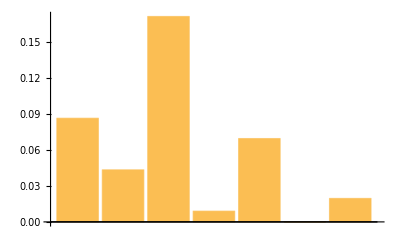

```mathematica
BarChart[OEEFull]
```

```mathematica
Export["all_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

all_recursion_frequencies_width3.png

```mathematica
width=4;
ics=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];
```

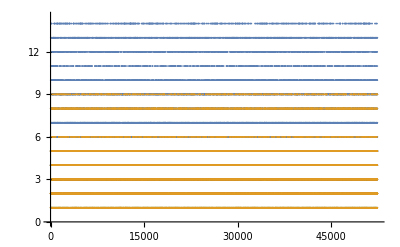

```mathematica
f[x_]:=x[[5]]
fullrec=f/@ics;
f[x_]:=x[[10]]
ostaterec=f/@ics;
f[x_]:=x[[11]]
orulerec=f/@ics;
f[x_]:=x[[12]]
estaterec=f/@ics;

ListPlot[{fullrec,estaterec}]
(*
ListLogLogPlot[{Sort[fullrec]//Reverse//Tally,Sort[ostaterec]//Reverse//Tally,Sort[orulerec]//Reverse//Tally,Sort[estaterec]//Reverse//Tally},PlotLabel->"All Recursion Frequencies (Full E), Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Full Rec","O State Rec","R State Rec"}]*)
```

```mathematica
Export["all_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

all_recursion_frequencies_width4.png

```mathematica
width=5;
ics=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];
```

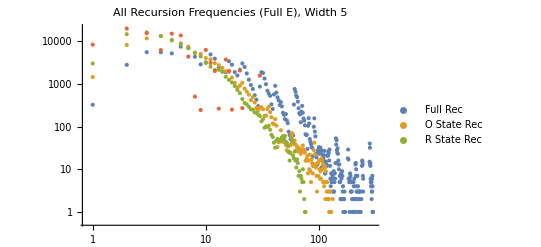

```mathematica
f[x_]:=x[[5]]
fullrec=f/@ics;
f[x_]:=x[[10]]
ostaterec=f/@ics;
f[x_]:=x[[11]]
orulerec=f/@ics;
f[x_]:=x[[12]]
estaterec=f/@ics;
ListLogLogPlot[{Sort[fullrec]//Reverse//Tally,Sort[ostaterec]//Reverse//Tally,Sort[orulerec]//Reverse//Tally,Sort[estaterec]//Reverse//Tally},PlotRange->All,PlotLabel->"All Recursion Frequencies (Full E), Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Full Rec","O State Rec","R State Rec"}]
```

```mathematica
Export["all_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

all_recursion_frequencies_width5.png

```mathematica
width=6;
ics=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];
```

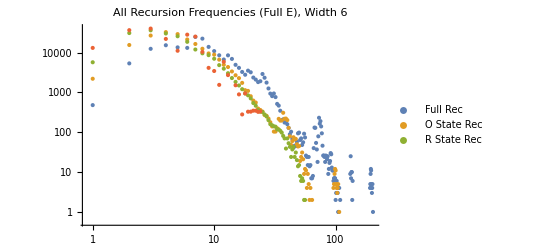

```mathematica
f[x_]:=x[[5]]
fullrec=f/@ics;
f[x_]:=x[[10]]
ostaterec=f/@ics;
f[x_]:=x[[11]]
orulerec=f/@ics;
f[x_]:=x[[12]]
estaterec=f/@ics;
ListLogLogPlot[{Sort[fullrec]//Reverse//Tally,Sort[ostaterec]//Reverse//Tally,Sort[orulerec]//Reverse//Tally,Sort[estaterec]//Reverse//Tally},PlotRange->All,PlotLabel->"All Recursion Frequencies (Full E), Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Full Rec","O State Rec","R State Rec"}]
```

```mathematica
Export["all_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

all_recursion_frequencies_width6.png

```mathematica
width=7;
ics=Join[Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]];
```

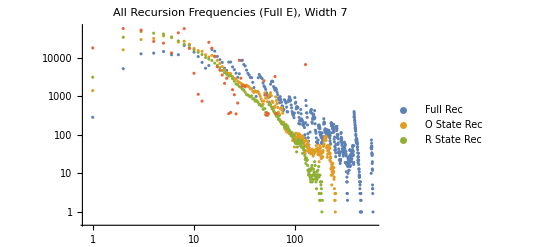

```mathematica
f[x_]:=x[[5]]
fullrec=f/@ics;
f[x_]:=x[[10]]
ostaterec=f/@ics;
f[x_]:=x[[11]]
orulerec=f/@ics;
f[x_]:=x[[12]]
estaterec=f/@ics;
ListLogLogPlot[{Sort[fullrec]//Reverse//Tally,Sort[ostaterec]//Reverse//Tally,Sort[orulerec]//Reverse//Tally,Sort[estaterec]//Reverse//Tally},PlotRange->All,PlotLabel->"All Recursion Frequencies (Full E), Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Full Rec","O State Rec","R State Rec"}]
```

```mathematica
Export["all_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

all_recursion_frequencies_width7.png

```mathematica
width=8;
ics=Join[Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]];
```

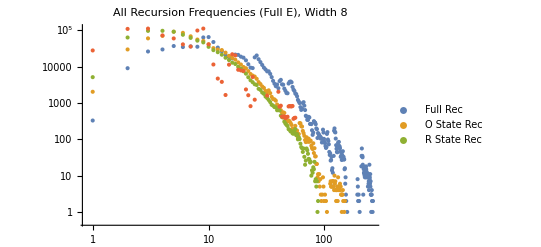

```mathematica
f[x_]:=x[[5]]
fullrec=f/@ics;
f[x_]:=x[[10]]
ostaterec=f/@ics;
f[x_]:=x[[11]]
orulerec=f/@ics;
f[x_]:=x[[12]]
estaterec=f/@ics;
ListLogLogPlot[{Sort[fullrec]//Reverse//Tally,Sort[ostaterec]//Reverse//Tally,Sort[orulerec]//Reverse//Tally,Sort[estaterec]//Reverse//Tally},PlotRange->All,PlotLabel->"All Recursion Frequencies (Full E), Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Full Rec","O State Rec","R State Rec"}]
```

```mathematica
Export["all_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

all_recursion_frequencies_width8.png

```mathematica
width=9;
ics=Join[Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]];
```

Part::partw: Part 5 of {434, 73, 253} does not exist.

Part::partw: Part 10 of {434, 73, 253} does not exist.

Part::partw: Part 11 of {434, 73, 253} does not exist.

Part::partw: Part 12 of {434, 73, 253} does not exist.

Part::partw: Part 5 of {434., 73., 253.} does not exist.

Part::partw: Part 10 of {434., 73., 253.} does not exist.

Part::partw: Part 11 of {434., 73., 253.} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

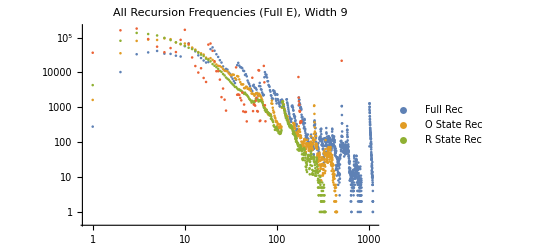

```mathematica
f[x_]:=x[[5]]
fullrec=f/@ics;
f[x_]:=x[[10]]
ostaterec=f/@ics;
f[x_]:=x[[11]]
orulerec=f/@ics;
f[x_]:=x[[12]]
estaterec=f/@ics;
ListLogLogPlot[{Sort[fullrec]//Reverse//Tally,Sort[ostaterec]//Reverse//Tally,Sort[orulerec]//Reverse//Tally,Sort[estaterec]//Reverse//Tally},PlotRange->All,PlotLabel->"All Recursion Frequencies (Full E), Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Full Rec","O State Rec","R State Rec"}]
```

```mathematica
Export["all_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

all_recursion_frequencies_width9.png

```mathematica
width=10;
ics=Join[Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-5_FullEFIXED.csv"],1]];
```

Part::partw: Part 10 of {169, 970, 87, 130, 16, 10, 2, 16, 5} does not exist.

Part::partw: Part 11 of {169, 970, 87, 130, 16, 10, 2, 16, 5} does not exist.

Part::partw: Part 12 of {169, 970, 87, 130, 16, 10, 2, 16, 5} does not exist.

Part::partw: Part 10 of {169., 970., 87., 130., 16., 10., 2., 16., 5.} does not exist.

Part::partw: Part 11 of {169., 970., 87., 130., 16., 10., 2., 16., 5.} does not exist.

Part::partw: Part 12 of {169., 970., 87., 130., 16., 10., 2., 16., 5.} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

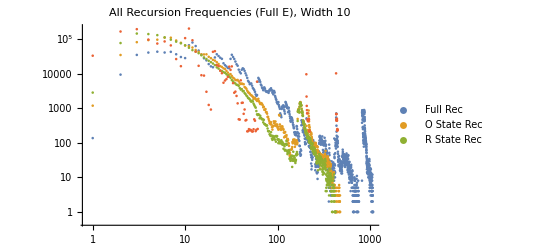

```mathematica
f[x_]:=x[[5]]
fullrec=f/@ics;
f[x_]:=x[[10]]
ostaterec=f/@ics;
f[x_]:=x[[11]]
orulerec=f/@ics;
f[x_]:=x[[12]]
estaterec=f/@ics;
ListLogLogPlot[{Sort[fullrec]//Reverse//Tally,Sort[ostaterec]//Reverse//Tally,Sort[orulerec]//Reverse//Tally,Sort[estaterec]//Reverse//Tally},PlotRange->All,PlotLabel->"All Recursion Frequencies (Full E), Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Full Rec","O State Rec","R State Rec"}]
```

```mathematica
Export["all_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

all_recursion_frequencies_width10.png

#### All E, state recurrences

```mathematica
width=3;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

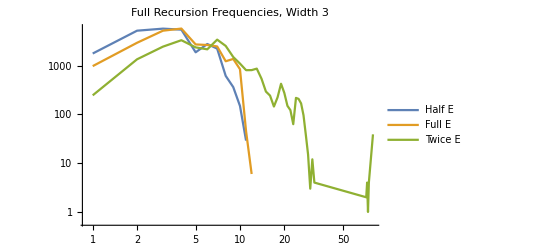

```mathematica
f[x_]:=x[[5]]
hrec=f/@icsh;

f[x_]:=x[[5]]
frec=f/@icsf;

f[x_]:=x[[5]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"Full Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["full_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

full_recursion_frequencies_width3.png

```mathematica
width=4;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

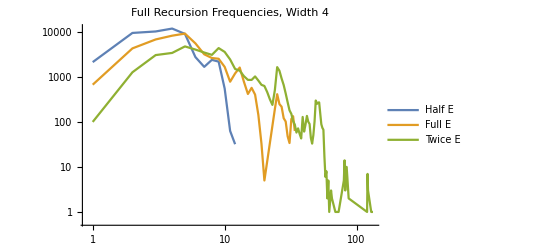

```mathematica
f[x_]:=x[[5]]
hrec=f/@icsh;

f[x_]:=x[[5]]
frec=f/@icsf;

f[x_]:=x[[5]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"Full Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["full_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

full_recursion_frequencies_width4.png

```mathematica
width=5;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

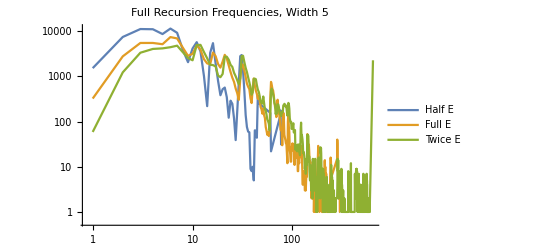

```mathematica
f[x_]:=x[[5]]
hrec=f/@icsh;

f[x_]:=x[[5]]
frec=f/@icsf;

f[x_]:=x[[5]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"Full Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"},PlotRange->All]
```

```mathematica
Export["full_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

full_recursion_frequencies_width5.png

```mathematica
width=6;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

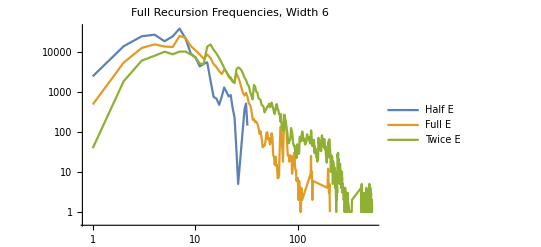

```mathematica
f[x_]:=x[[5]]
hrec=f/@icsh;

f[x_]:=x[[5]]
frec=f/@icsf;

f[x_]:=x[[5]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"Full Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"},PlotRange->All]
```

```mathematica
Export["full_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

full_recursion_frequencies_width6.png

```mathematica
width=7;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Join[Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

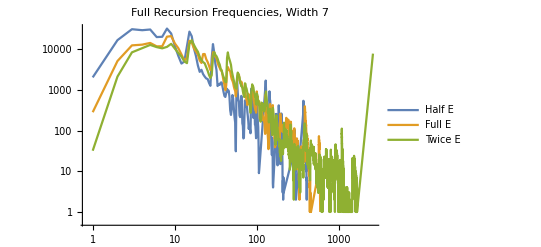

```mathematica
f[x_]:=x[[5]]
hrec=f/@icsh;

f[x_]:=x[[5]]
frec=f/@icsf;

f[x_]:=x[[5]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"Full Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"},PlotRange->All]
```

```mathematica
Export["full_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

full_recursion_frequencies_width7.png

```mathematica
width=8;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Join[Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

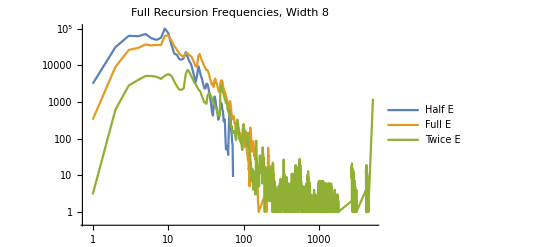

```mathematica
f[x_]:=x[[5]]
hrec=f/@icsh;

f[x_]:=x[[5]]
frec=f/@icsf;

f[x_]:=x[[5]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"Full Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"},PlotRange->All]
```

```mathematica
Export["full_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

full_recursion_frequencies_width8.png

#### All E, O state recurrences

```mathematica
width=3;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

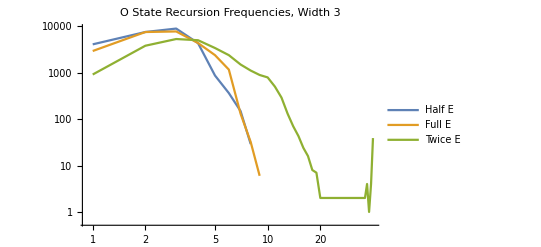

```mathematica
f[x_]:=x[[10]]
hrec=f/@icsh;

f[x_]:=x[[10]]
frec=f/@icsf;

f[x_]:=x[[10]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"O State Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["ostate_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

ostate_recursion_frequencies_width3.png

```mathematica
width=4;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

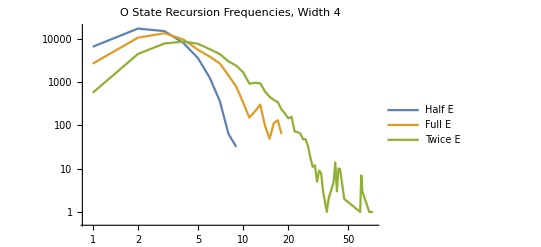

```mathematica
f[x_]:=x[[10]]
hrec=f/@icsh;

f[x_]:=x[[10]]
frec=f/@icsf;

f[x_]:=x[[10]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"O State Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["ostate_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

ostate_recursion_frequencies_width4.png

```mathematica
width=5;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

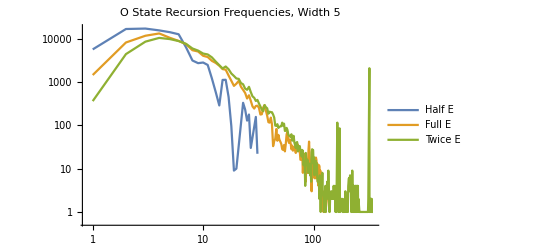

```mathematica
f[x_]:=x[[10]]
hrec=f/@icsh;

f[x_]:=x[[10]]
frec=f/@icsf;

f[x_]:=x[[10]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"O State Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["ostate_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

ostate_recursion_frequencies_width5.png

```mathematica
width=6;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

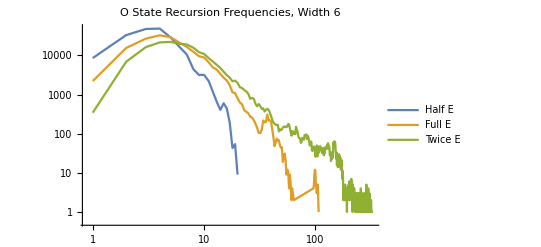

```mathematica
f[x_]:=x[[10]]
hrec=f/@icsh;

f[x_]:=x[[10]]
frec=f/@icsf;

f[x_]:=x[[10]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"O State Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["ostate_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

ostate_recursion_frequencies_width6.png

```mathematica
width=7;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Join[Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

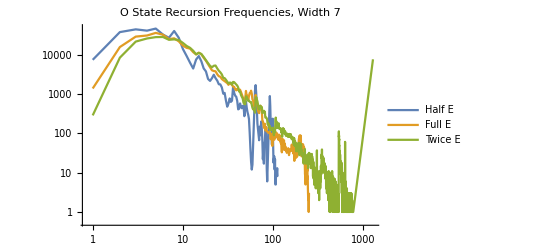

```mathematica
f[x_]:=x[[10]]
hrec=f/@icsh;

f[x_]:=x[[10]]
frec=f/@icsf;

f[x_]:=x[[10]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"O State Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["ostate_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

ostate_recursion_frequencies_width7.png

```mathematica
width=8;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Join[Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

Part::partw: Part 10 of {31340, 32, 28, 184, 12} does not exist.

Part::partw: Part 10 of {31340., 32., 28., 184., 12.} does not exist.

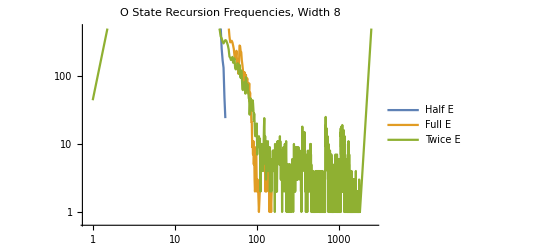

```mathematica
f[x_]:=x[[10]]
hrec=f/@icsh;

f[x_]:=x[[10]]
frec=f/@icsf;

f[x_]:=x[[10]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"O State Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["ostate_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

ostate_recursion_frequencies_width8.png

#### All E, O rule recurrences

```mathematica
width=3;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

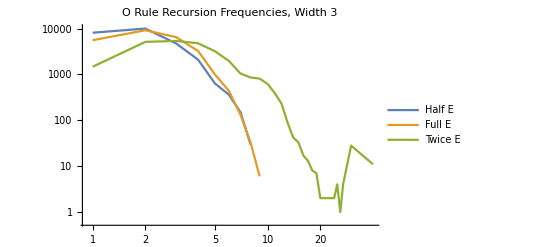

```mathematica
f[x_]:=x[[11]]
hrec=f/@icsh;

f[x_]:=x[[11]]
frec=f/@icsf;

f[x_]:=x[[11]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"O Rule Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["orule_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

orule_recursion_frequencies_width3.png

```mathematica
width=4;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

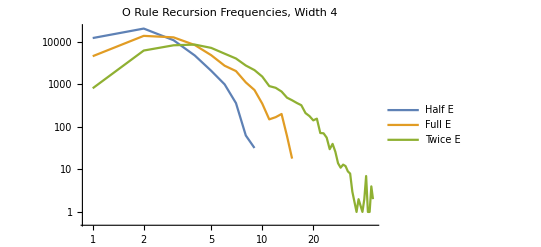

```mathematica
f[x_]:=x[[11]]
hrec=f/@icsh;

f[x_]:=x[[11]]
frec=f/@icsf;

f[x_]:=x[[11]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"O Rule Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["orule_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

orule_recursion_frequencies_width4.png

```mathematica
width=5;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

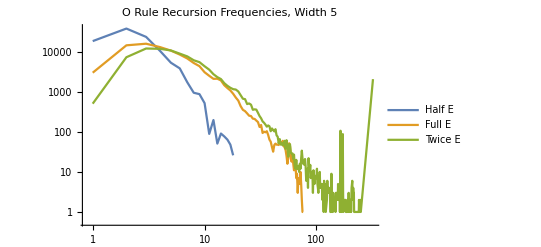

```mathematica
f[x_]:=x[[11]]
hrec=f/@icsh;

f[x_]:=x[[11]]
frec=f/@icsf;

f[x_]:=x[[11]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"O Rule Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["orule_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

orule_recursion_frequencies_width5.png

```mathematica
width=6;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

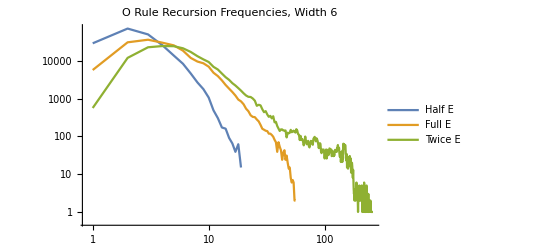

```mathematica
f[x_]:=x[[11]]
hrec=f/@icsh;

f[x_]:=x[[11]]
frec=f/@icsf;

f[x_]:=x[[11]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"O Rule Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["orule_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

orule_recursion_frequencies_width6.png

```mathematica
width=7;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Join[Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

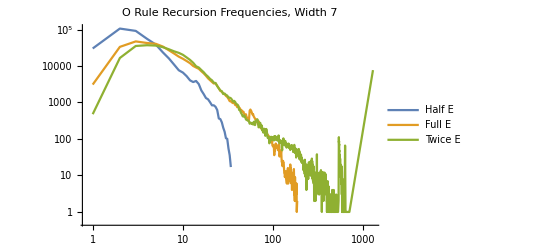

```mathematica
f[x_]:=x[[11]]
hrec=f/@icsh;

f[x_]:=x[[11]]
frec=f/@icsf;

f[x_]:=x[[11]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"O Rule Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["orule_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

orule_recursion_frequencies_width7.png

```mathematica
width=8;
icsh=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];

icsf=Join[Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]];

icst=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
```

Part::partw: Part 11 of {31340, 32, 28, 184, 12} does not exist.

Part::partw: Part 11 of {31340., 32., 28., 184., 12.} does not exist.

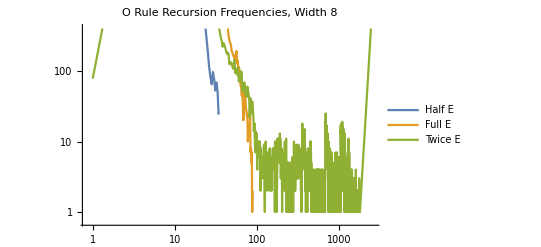

```mathematica
f[x_]:=x[[11]]
hrec=f/@icsh;

f[x_]:=x[[11]]
frec=f/@icsf;

f[x_]:=x[[11]]
trec=f/@icst;

ListLogLogPlot[{Sort[hrec]//Reverse//Tally,Sort[frec]//Reverse//Tally,Sort[trec]//Reverse//Tally},Joined->True,PlotLabel->"O Rule Recursion Frequencies, Width "<>ToString[width],GridLines->{{{2^width,Red}},None},PlotLegends->{"Half E","Full E","Twice E"}]
```

```mathematica
Export["orule_recursion_frequencies_width"<>ToString[width]<>".png",%]
```

orule_recursion_frequencies_width8.png

### Difference in recursion times between the Environment and Organism (states only)

#### HalfE

```mathematica
width=3;
in=Import["Width"<>ToString[width]<>"AttractorStats_HalfE_FINAL.csv"];
```

eIC,oIC,erule,orule,ics[[m]][[6]],compression,fit,mutationpercent,Tally[CAorganism],Tally[organismrules]

```mathematica
ToExpression[in[[1]][[7]]][[1]][[2]]
```

```mathematica
in[[1]][[5]]
```

3

```mathematica
%[[1]]
```

k

```mathematica
Table[
width=i;
in=Import["Width"<>ToString[width]<>"AttractorStats_TwiceE_FINAL.csv"];
in2=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-"<>ToString[0]<>"_TwiceE.csv"],1];
f[x_]:=x[[6]];
g[x_]:=x[[5]];
comp=f/@in;
rec=g/@in;
fullrec=g/@in2;
z[x_]:={First[x],100*(Last[x]/Length[comp])};
lyp=Table[ToExpression[in[[x]][[7]]][[1]][[2]],{x,1,Length[in]}];
compdist=SortBy[z/@Tally[comp],First];
compare=Transpose[{rec,comp}];
compare2=Transpose[{rec,lyp}];
compare3=Transpose[{fullrec,comp}];
compare4=Transpose[{fullrec,lyp}];
k[x_]:={First[x],Last[x]/Length[lyp]};
lypdist=Last/@SortBy[lyp//Tally,First]//Sort//Reverse;
compdist2=Last/@SortBy[comp//Tally,First]//Sort//Reverse;

plots1=
Grid[{
{Text[Style["Complexity Measures: w = "<>ToString[width]<>", w_e = 2w","Label",18,GrayLevel[0.4],Italic]],SpanFromLeft},

{
ListLogPlot[compdist,PlotTheme->{"Business","PlotMarkers","PastelColor","MediumLines","Square"},PlotRange->Full,Joined->True,Frame->True,FrameLabel->{"C","% Occurences (Log)"},ImageSize->Small],

ListLogLogPlot[compdist2,PlotTheme->{"Business","PlotMarkers","PastelColor","MediumLines","Square"},PlotRange->Full,Frame->True,FrameLabel->{"Rank(C) (Log)","Occurences (Log)"},ImageSize->Small],

ListLogLogPlot[compare,PlotTheme->{"Business","PlotMarkers","PastelColor","Square"},PlotRange->Full,Frame->True,FrameLabel->{"Attractor Size (Log)","C (Log)"},ImageSize->Small],

ListLogLogPlot[compare3,PlotTheme->{"Business","PlotMarkers","PastelColor","Square"},PlotRange->Full,Frame->True,FrameLabel->{"Recurrence (Log)","C (Log)"},ImageSize->Small]
},

{
Histogram[lyp,ScalingFunctions->"Log",PlotTheme->{"Business","PastelColor","Square"},PlotRange->All,Frame->True,FrameLabel->{"λ","Occurences (Log)"},ImageSize->Small],

ListLogLogPlot[lypdist,PlotTheme->{"Business","PlotMarkers","PastelColor","MediumLines","Square"},PlotRange->Full,Frame->True,FrameLabel->{"Rank(λ) (Log)","Occurences (Log)"},ImageSize->Small],

ListPlot[compare2,PlotTheme->{"Business","PlotMarkers","PastelColor","Square"},Frame->True,FrameLabel->{"Attractor Size","λ"},ImageSize->Small],

ListPlot[compare4,PlotTheme->{"Business","PlotMarkers","PastelColor","Square"},Frame->True,FrameLabel->{"Recurrence","λ"},ImageSize->Small]
}},Spacings->{4, 2},Frame->True];


plots2=
Grid[{
{Text[Style["Recursion: w = "<>ToString[width]<>", w_e = 2w","Label",18,GrayLevel[0.4],Italic]],SpanFromLeft},

{
Histogram[rec,ScalingFunctions->"Log",PlotTheme->{"Business","PastelColor","Square"},PlotRange->All,Frame->True,FrameLabel->{"Attractor Size","Occurences (Log)"},ImageSize->Small],
Histogram[fullrec,ScalingFunctions->"Log",PlotTheme->{"Business","PastelColor","Square"},PlotRange->All,Frame->True,FrameLabel->{"Recurrence","Occurences (Log)"},ImageSize->Small]
}},Spacings->{4, 2},Frame->True];

Export["Width"<>ToString[width]<>"Complexity_Twice.pdf",plots1];
Export["Width"<>ToString[width]<>"Recursion_Twice.pdf",plots2];

,{i,3,6}];
```

#### Lyp and C value distributions

```mathematica
Table[
width=i;
in=Import["Width"<>ToString[width]<>"AttractorStats_TwiceE_FINAL.csv"];
in2=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-"<>ToString[0]<>"_TwiceE.csv"],1];
f[x_]:=x[[6]];
g[x_]:=x[[5]];
comp=f/@in;
rec=g/@in;
fullrec=g/@in2;
z[x_]:={First[x],100*(Last[x]/Length[comp])};
lyp=Table[ToExpression[in[[x]][[7]]][[1]][[2]],{x,1,Length[in]}];
compdist=SortBy[z/@Tally[comp],First];
compare=Transpose[{rec,comp}];
compare2=Transpose[{rec,lyp}];
compare3=Transpose[{fullrec,comp}];
compare4=Transpose[{fullrec,lyp}];
k[x_]:={First[x],Last[x]/Length[lyp]};
lypdist=Last/@SortBy[lyp//Tally,First]//Sort//Reverse;
compdist2=Last/@SortBy[comp//Tally,First]//Sort//Reverse;

plots1=
Grid[{
{Text[Style["Complexity Measures: w = "<>ToString[width]<>", w_e = 2w","Label",18,GrayLevel[0.4],Italic]],SpanFromLeft},

{
ListLogPlot[compdist,PlotTheme->{"Business","PlotMarkers","PastelColor","MediumLines","Square"},PlotRange->Full,Joined->True,Frame->True,FrameLabel->{"C","% Occurences (Log)"},ImageSize->Small],

ListLogLogPlot[compdist2,PlotTheme->{"Business","PlotMarkers","PastelColor","MediumLines","Square"},PlotRange->Full,Frame->True,FrameLabel->{"Rank(C) (Log)","Occurences (Log)"},ImageSize->Small],

ListLogLogPlot[compare,PlotTheme->{"Business","PlotMarkers","PastelColor","Square"},PlotRange->Full,Frame->True,FrameLabel->{"Attractor Size (Log)","C (Log)"},ImageSize->Small],

ListLogLogPlot[compare3,PlotTheme->{"Business","PlotMarkers","PastelColor","Square"},PlotRange->Full,Frame->True,FrameLabel->{"Recurrence (Log)","C (Log)"},ImageSize->Small]
},

{
Histogram[lyp,ScalingFunctions->"Log",PlotTheme->{"Business","PastelColor","Square"},PlotRange->All,Frame->True,FrameLabel->{"λ","Occurences (Log)"},ImageSize->Small],

ListLogLogPlot[lypdist,PlotTheme->{"Business","PlotMarkers","PastelColor","MediumLines","Square"},PlotRange->Full,Frame->True,FrameLabel->{"Rank(λ) (Log)","Occurences (Log)"},ImageSize->Small]
}},Spacings->{4, 2},Frame->True];


plots2=
Grid[{
{Text[Style["Recursion: w = "<>ToString[width]<>", w_e = 2w","Label",18,GrayLevel[0.4],Italic]],SpanFromLeft},

{
Histogram[rec,ScalingFunctions->"Log",PlotTheme->{"Business","PastelColor","Square"},PlotRange->All,Frame->True,FrameLabel->{"Attractor Size","Occurences (Log)"},ImageSize->Small],
Histogram[fullrec,ScalingFunctions->"Log",PlotTheme->{"Business","PastelColor","Square"},PlotRange->All,Frame->True,FrameLabel->{"Recurrence","Occurences (Log)"},ImageSize->Small]
}},Spacings->{4, 2},Frame->True];
(*
Export["Width"<>ToString[width]<>"Complexity_Twice.pdf",plots1];
Export["Width"<>ToString[width]<>"Recursion_Twice.pdf",plots2];
*)
{plots1,plots2}
,{i,3,3}]
```

```mathematica
f[x_]:={x[[1]],x[[2]]/Length[lyp]}
f/@SortBy[Round[lyp,0.1]//Tally,First];
```

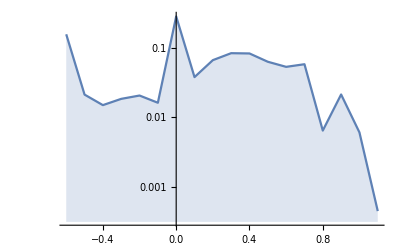

```mathematica
ListLogPlot[f/@SortBy[Round[lyp,0.1]//Tally,First],Joined->True,Filling->Bottom,PlotRange->All]
```

```mathematica
Table[
width=i;
inh=Import["Width"<>ToString[width]<>"AttractorStats_HalfE_FINAL.csv"];
inf=Import["Width"<>ToString[width]<>"AttractorStats_FullE_FINAL.csv"];
int=Import["Width"<>ToString[width]<>"AttractorStats_TwiceE_FINAL.csv"];
ini=Import["Width"<>ToString[width]<>"AttractorStats_Iso_FINAL.csv"];
(*inh[[x]][[7]]][[1]][[2]]*)
lyph=Table[ToExpression[inh[[x]][[6]]],{x,1,Length[inh]}];
lypf=Table[ToExpression[inf[[x]][[6]]],{x,1,Length[inf]}];
lypt=Table[ToExpression[int[[x]][[6]]],{x,1,Length[int]}];
lypi=Table[ToExpression[ini[[x]][[6]]],{x,1,Length[ini]}];
plot=Histogram[{lypt,lypf,lyph,lypi},{0.1},"Probability",PlotRange->{{0.2,1.1},All},Frame->True,ChartLayout->"Stacked",FrameLabel->{"C Value","% Occurences (stacked)"},PlotLabel->Style["w = "<>ToString[width],"Label",16,GrayLevel[0.4]],FrameTicks->{{Automatic,None},{Automatic,None}},(*GridLines->{{{0,{Thick,Black}},{1,{Thick,Black}}},Automatic},*)ChartLegends->{"w_e = 2w","w_e = w","w_e = w/2","Isolated"}];

Export["Width"<>ToString[width]<>"CompDistribution.pdf",plot];
,{i,5,5}]
```

{Null}

#### %OEE

```mathematica
Table[
width=j;
in=Drop[Import["Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-"<>ToString[0]<>"_TwiceE.csv"],1];
f[x_]:=x[[5]];
in2=f/@in//Tally;
(DeleteCases[Table[
If[in2[[k]][[1]]≥ 2^width,in2[[k]][[2]]],{k,1,Length[in2]}],Null]//Total)/Length[in]
,{j,3,8}]
```

{10915/26214,14013/52429,15699/52429,10606/209715,20642/209715,1438/31961}

### Fun Pictures

{-Graphics-}

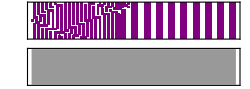

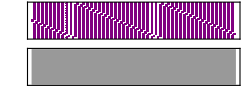

```mathematica
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

width=21;
envsize=Round[width];
timesteps=100;

PRT=
Table[

erule=RandomInteger[255];
orule=RandomInteger[255];
eIC={0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0};
oIC={0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0};

(*****environment setup*****)
environment=CellularAutomaton[erule,eIC,timesteps-1];
partitions[i_]:=Tally[Partition[environment[[i]],3,1]];
numberofpartitions[i_]:=Length[Tally[Partition[environment[[i]],3,1]]];

(*****organism setup*****)
state=oIC;
initialstate=state;
rule=ruletable[[orule+1]];


(******Check to change rule at every time step******)
smallsteps=

Table[
(*Before the mutation*)
ruleone=rule;
stateone=state;
(*Calulate the triplet freq distribution for both, boundaries are periodic. Fullcompare is to GatherBy triplet and flatten. It keeps the order to E triplets and O triplets. Only select the triplet dists that are in both E and O*)
orgthresholds1=Tally[Partition[state,3,1,1]];
thresholds1=Tally[Partition[environment[[j]],3,1,1]];
yo[x_]:=ReplacePart[x,2->x[[2]]/width];
ye[x_]:=ReplacePart[x,2->x[[2]]/envsize];
orgthresholds=yo/@orgthresholds1;
thresholds=ye/@thresholds1;
fullcompare=Flatten[Select[GatherBy[Join[thresholds,orgthresholds],First],Length[#]>1&]];
(*If there are triplets that appeared in both,*)
If[Length[fullcompare]>0,
(*Make a list from fullcompare, take every 4, so it is the distribution of triplets EOEOEO*)
comparethetwo=Take[Flatten[Select[GatherBy[Join[thresholds,orgthresholds],First],Length[#]>1&]],{4,-1,4}];
(*Their repspective triplets, labeled from 1 to 8*)
subrules2test=Flatten[Table[Position[subrules,fullcompare[[(1+8*(i-1));;((i-1)*8+3)]]],{i,1,Length[comparethetwo]/2}]];
(*If E≤0 for each successive pair in EOEOEO, then change the rule at the corresponding triplet site in the rule table. Subrulereplacements are the triplet replacements*)
subrulereplacements=
If[Length[subrules2test]>0,
Table[
If[comparethetwo[[2*i-1]]≤comparethetwo[[2*i]],
If[rule[[subrules2test[[i]],2]]==0,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]],
If[rule[[subrules2test[[i]],2]]==1,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]]]
,{i,1,Length[subrules2test]}]];
(*Put these replacements in the rule, making a new rule.*)
newrule=ReplacePart[rule,Rule@@@Transpose[{subrules2test,subrulereplacements}]];
(*Apply the rule to the state*)
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;
,

(*If there is nothing in fullcompare (there are no triplets that are similar in E and O), then apply the old rule*)
step=Nest[Partition[#,3,1,2]/.rule&,state,1];
state=step;
];

{stateone->state,8-(Intersection[ruleone,rule]//Length),FromDigits[Last/@ruleone,2]->FromDigits[Last/@rule,2]}

,{j,1,timesteps}];


(******Raw Data*******)
CAorganism=First/@First/@smallsteps;
organismrules=First/@Last/@smallsteps;

ArrayPlot[CAorganism]

,{m,1,1}]

one=Sound[SoundNote[#,0.25]&/@(Pick[Range[0,20]-2,#,1]&/@CAorganism)]
two=Sound[SoundNote[#,0.25]&/@(Pick[Range[0,20],#,1]&/@CellularAutomaton[erule,eIC,timesteps])]
```

```mathematica
Export["env7.mid",two]
```

env7.mid

### No Self-Reference

```mathematica
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

width=5;
envsize=Round[width];
timesteps=2^width;
```

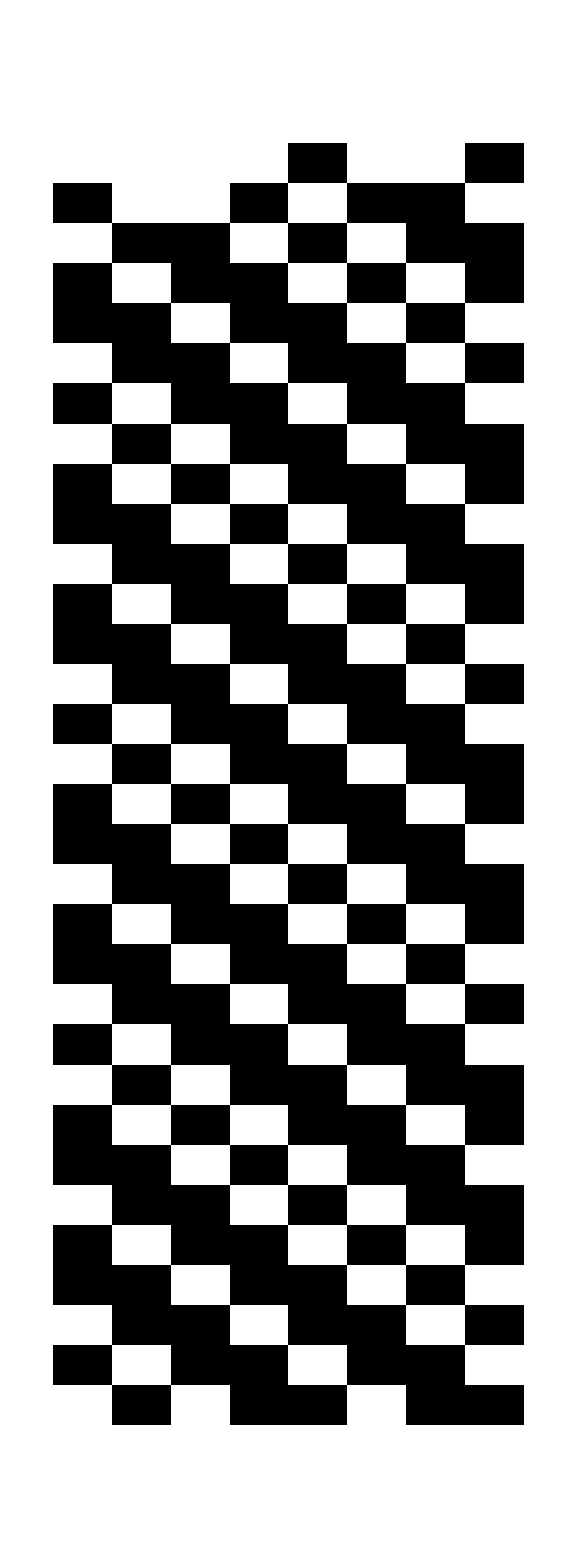
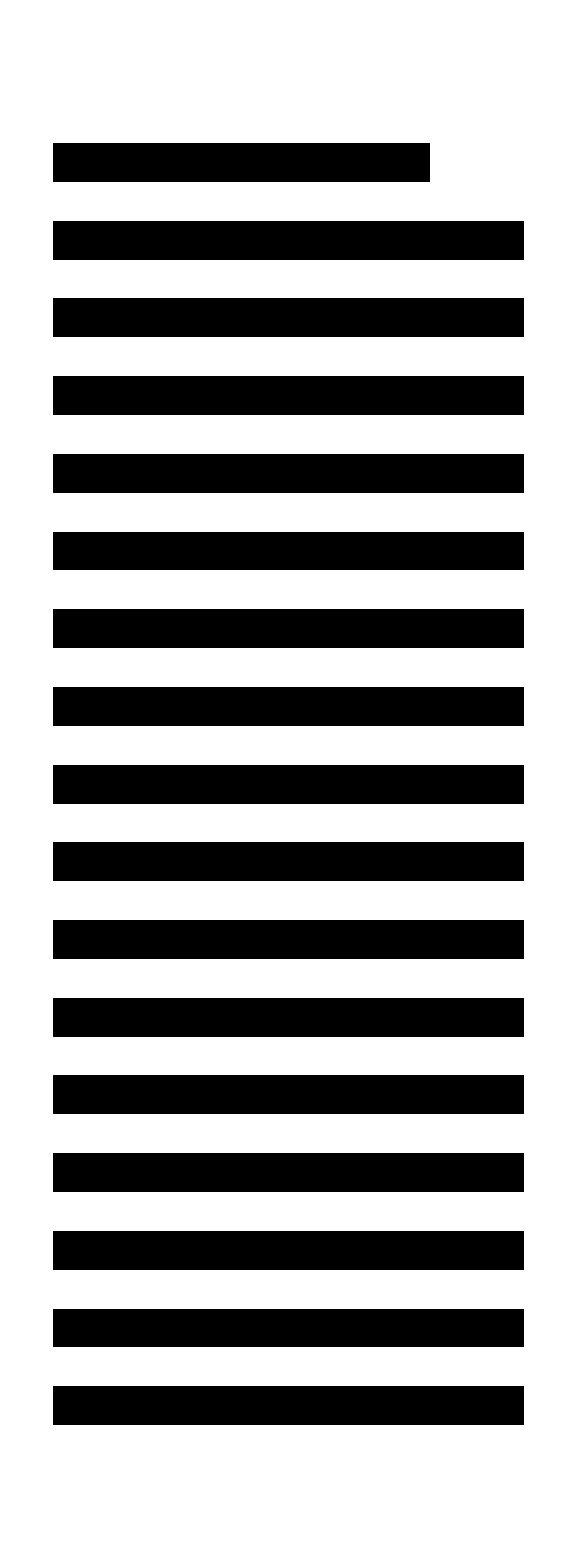
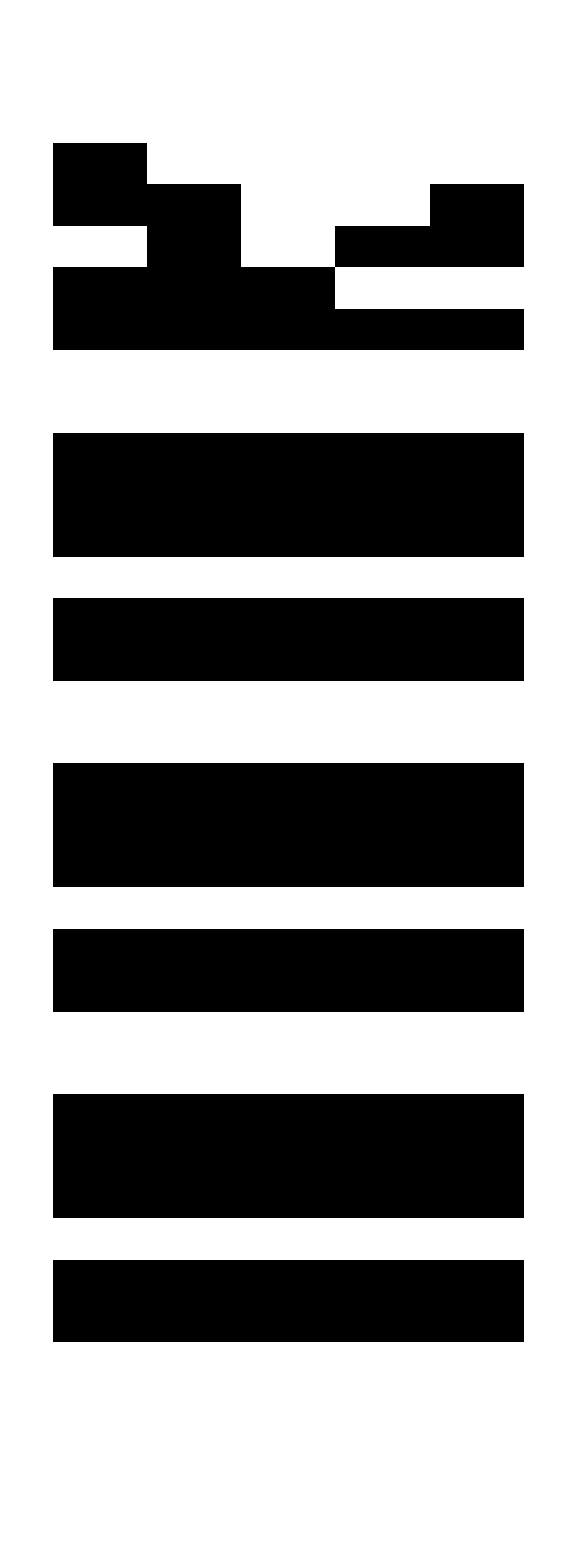
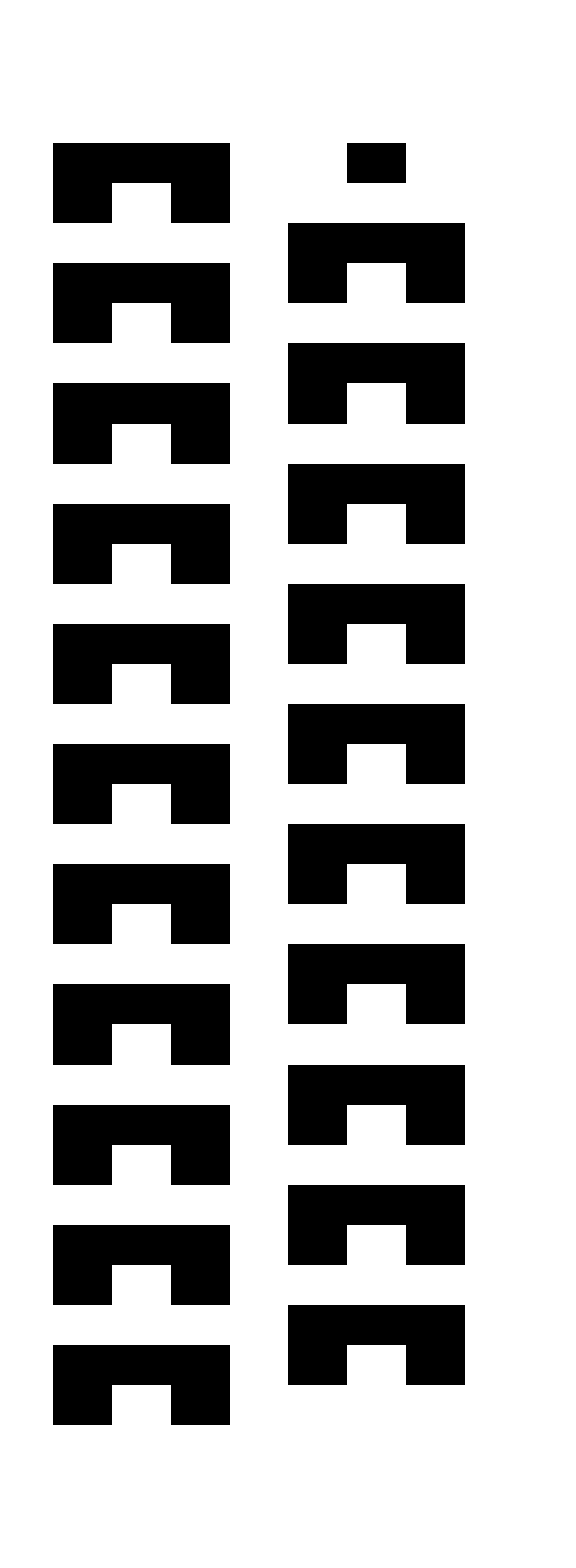
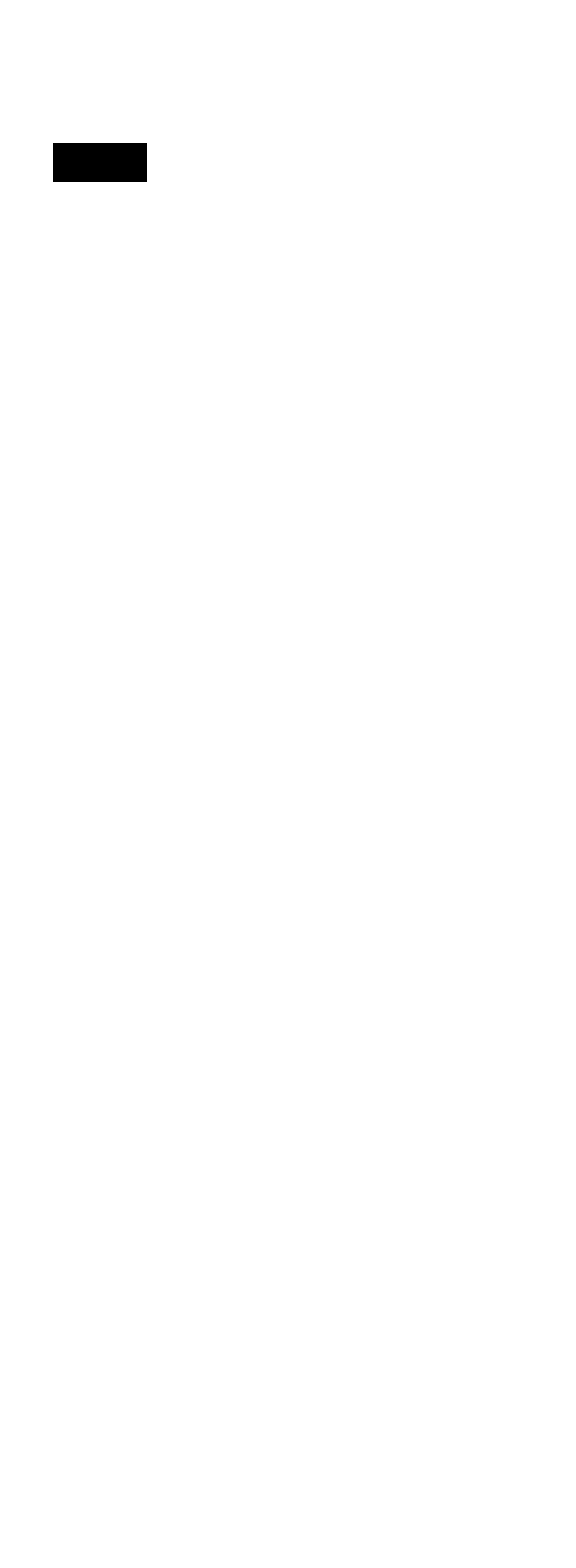
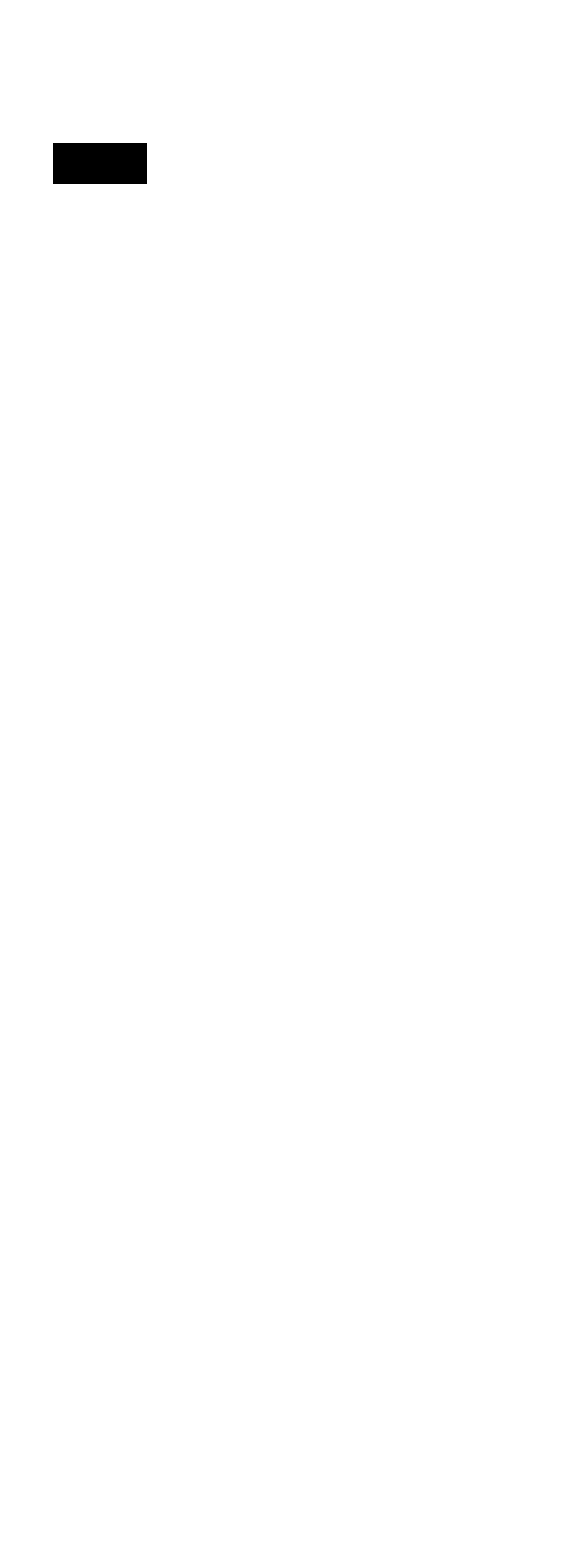
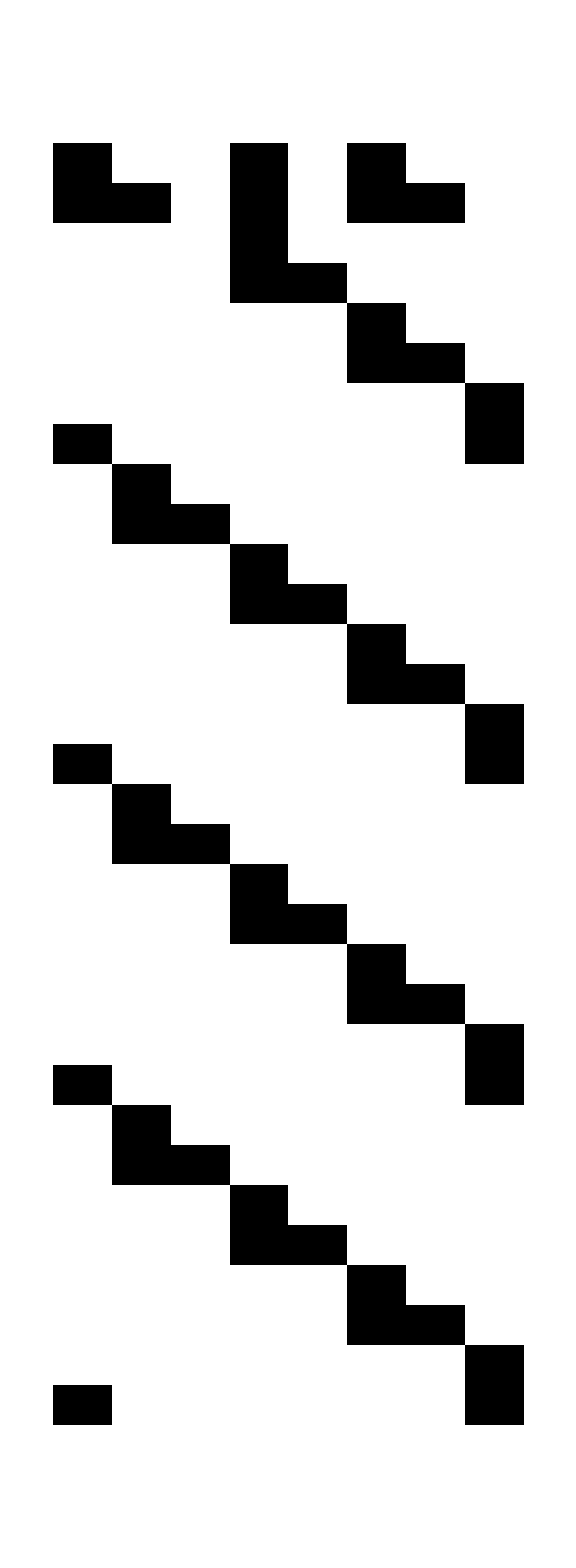
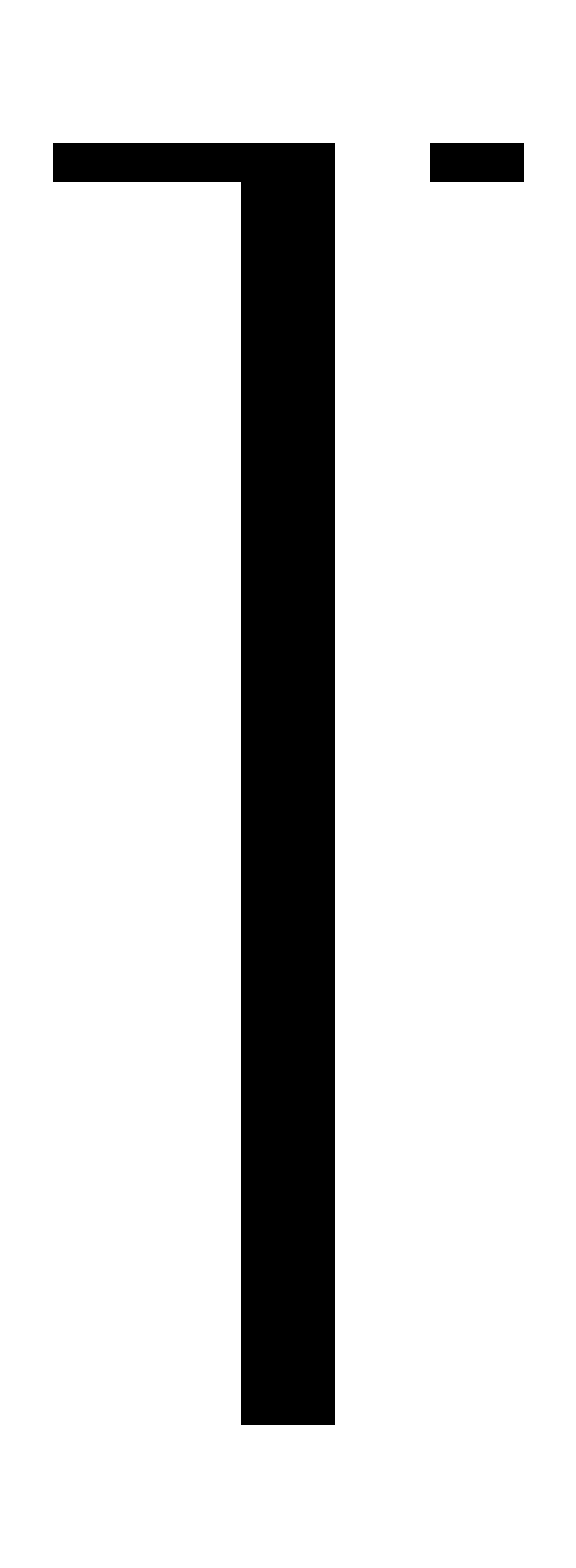
{-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-}

```mathematica
PRT=
Table[

erule=RandomInteger[255];
orule=RandomInteger[255];
eIC=RandomChoice[{0,1},8];
oIC=RandomChoice[{0,1},width];

(*****environment setup*****)
environment=CellularAutomaton[erule,eIC,timesteps-1];
f[x_]:=FromDigits[x,2];
erules=f/@environment;

(*****organism setup*****)
state=oIC;
initialstate=state;
rule=ruletable[[orule+1]];

CA=Table[
newstate=CellularAutomaton[erules[[t]],state,1]//Last;
state=newstate
,{t,1,timesteps-1}];

Row[{ArrayPlot[environment,ImageSize->Large],ArrayPlot[CellularAutomaton[orule,oIC,timesteps],ImageSize->Large],ArrayPlot[CA,ImageSize->Large]}]
,{m,1,100}]
```

```mathematica
Export["posterCAbig2.pdf",%]
```

posterCAbig2.pdf

## New Plots

### Recurrence Times

#### Organism State Recurrence

Run this 5 different times, and save each plot to a variable

```mathematica
width=3;
icsf=

(*
Flatten[{Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]},1];
*)


Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];


icst=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
icsh=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];
icsi=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Isolated_Organisms_AllCases-0_Iso.csv"],1];
```

```mathematica
f[x_]:=x[[10]];
ostaterecf=f/@icsf;
ostaterect=f/@icst;
ostaterech=f/@icsh;
f[x_]:=x[[5]];
ostatereci=f/@icsi;

w3=ListLogLogPlot[{Transpose[{First/@((Sort[ostaterech]//Reverse)/width^2//Tally),Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostaterecf]//Reverse)/2^width//Tally),Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostaterect]//Reverse)/2^width//Tally),Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostatereci]//Reverse)/2^width//Tally),Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)]}]},PlotRange->All,PlotLabel->"w = "<>ToString[width],Joined->False,Frame->True,FrameLabel->{"Log ( t_r/T_r )","Log ( % Frequency )"},LabelStyle->Directive[Black,FontFamily->"Helvetica"],GridLines->{{{1,{Red,Thick}}},None},PlotTheme->{"Scientific","BoldColor"}]
```

-Graphics-

Then export, only after I’m happy with the way they look

```mathematica
Export["w8_state_rec.pdf",w8]
```

w8_state_rec.pdf

#### Organism Rule Recurrence

Run this 6 different times, and save each plot to a variable

```mathematica
width=8;
icsf=


Flatten[{Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]},1];

(*

Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];
*)

icst=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
icsh=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];
icsi=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Isolated_Organisms_AllCases-0_Iso.csv"],1];
```

```mathematica
f[x_]:=x[[11]];
ostaterecf=f/@icsf;
ostaterect=f/@icst;
ostaterech=f/@icsh;
ostatereci=ConstantArray[1,Length[icsi]];

w8=ListLogLogPlot[{Transpose[{First/@((Sort[ostaterech]//Reverse)/width^2//Tally),Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostaterecf]//Reverse)/2^width//Tally),Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostaterect]//Reverse)/2^width//Tally),Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostatereci]//Reverse)/2^width//Tally),Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)]}]},PlotRange->All,PlotLabel->"w = "<>ToString[width],Joined->False,Frame->True,FrameLabel->{"Log ( t_r/T_r )","Log ( % Frequency )"},LabelStyle->Directive[Black,FontFamily->"Helvetica"],GridLines->{{{1,{Red,Thick}}},None},PlotTheme->{"Scientific","BoldColor"}]
```

Part::partw: Part 11 of {31340, 32, 28, 184, 12} does not exist.

Part::partw: Part 11 of {31340., 32., 28., 184., 12.} does not exist.

-Graphics-

Then export, only after I’m happy with the way they look

```mathematica
Export["w3_rule_rec.pdf",w3]
```

w3_rule_rec.pdf

#### Organism Attractor Size (includes rule and state) histograms

Run this 6 different times, and save each plot to a variable

```mathematica
width=3;
icsf=

(*
Flatten[{Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]},1];
*)

Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];


icst=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
icsh=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];
icsi=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Isolated_Organisms_AllCases-0_Iso.csv"],1];
```

```mathematica
f[x_]:=x[[6]];
ostaterecf=f/@icsf;
ostaterect=f/@icst;
ostaterech=f/@icsh;
f[x_]:=x[[6]];
ostatereci=f/@icsi;

w8=ListLogLogPlot[{Transpose[{First/@((Sort[ostaterech]//Reverse)/width^2//Tally),Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostaterecf]//Reverse)/2^width//Tally),Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostaterect]//Reverse)/2^width//Tally),Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostatereci]//Reverse)/2^width//Tally),Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)]}]},PlotRange->All,PlotLabel->"w = "<>ToString[width],Joined->False,Frame->True,FrameLabel->{"Log ( t_a/T_r )","Log ( % Frequency )"},LabelStyle->Directive[Black,FontFamily->"Helvetica"],GridLines->{{{1,{Red,Thick}}},None},PlotTheme->{"Scientific","BoldColor"}]
```

-Graphics-

Then export, only after I’m happy with the way they look

```mathematica
Export["w8_att_hist.pdf",w8]
```

w8_att_hist.pdf

#### Organism Attractor Size (includes rule and state) rank order

Run this 6 different times, and save each plot to a variable

```mathematica
width=8;
icsf=


Flatten[{Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]},1];
(*

Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];
*)

icst=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
icsh=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];
icsi=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Isolated_Organisms_AllCases-0_Iso.csv"],1];
```

```mathematica
f[x_]:=x[[6]];
ostaterecf=f/@icsf;
ostaterect=f/@icst;
ostaterech=f/@icsh;
f[x_]:=x[[6]];
ostatereci=f/@icsi;

w8=ListLogLogPlot[
{(Last/@SortBy[(Sort[ostaterech]//Reverse)/width^2//Tally,Last])//Sort//Reverse,(Last/@SortBy[(Sort[ostaterecf]//Reverse)/width^2//Tally,Last])//Sort//Reverse,(Last/@SortBy[(Sort[ostaterect]//Reverse)/width^2//Tally,Last])//Sort//Reverse,(Last/@SortBy[(Sort[ostatereci]//Reverse)/width^2//Tally,Last])//Sort//Reverse},PlotRange->All,PlotLabel->"w = "<>ToString[width],Joined->True,Frame->True,FrameLabel->{"Rank t_a/T_r","Log ( % Frequency )"},LabelStyle->Directive[Black,FontFamily->"Helvetica"],PlotTheme->{"Scientific","BoldColor"}]
```

Part::partw: Part 6 of {31340, 32, 28, 184, 12} does not exist.

-Graphics-

Then export, only after I’m happy with the way they look

```mathematica
Export["w4_att_rank.pdf",w4]
```

w4_att_rank.pdf

```mathematica
(Last/@SortBy[(Sort[ostaterech]//Reverse)/width^2//Tally,Last])//Sort//Reverse
```

{8547,7217,6042,4408}

{{2/3,1/3,2/9,1/9},{1007/4369,2849/8738,2204/13107,7217/26214}}

#### Organism Rule Recurrence (w vs Max recursion & w vs Max freq)

Run this 6 different times, and save each plot to a variable

```mathematica
width=8;
icsf=

Flatten[{Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]},1];
(*
Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];
*)
icst=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
icsh=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];
icsi=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Isolated_Organisms_AllCases-0_Iso.csv"],1];

f[x_]:=x[[11]];
ostaterecf=f/@icsf;
ostaterect=f/@icst;
ostaterech=f/@icsh;
ostatereci=ConstantArray[1,Length[icsi]];

maxrec8h=SortBy[Transpose[{First/@((Sort[ostaterech]//Reverse)/width^2//Tally),Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)]}],First]//Last;
maxrec8f=SortBy[Transpose[{First/@((Sort[ostaterecf]//Reverse)/width^2//Tally),Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)]}],First]//Last;
maxrec8t=SortBy[Transpose[{First/@((Sort[ostaterect]//Reverse)/width^2//Tally),Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)]}],First]//Last;
maxrec8i=SortBy[Transpose[{First/@((Sort[ostatereci]//Reverse)/width^2//Tally),Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)]}],First]//Last;
maxfreq8h=SortBy[Transpose[{First/@((Sort[ostaterech]//Reverse)/width^2//Tally),Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)]}],Last]//Last;
maxfreq8f=SortBy[Transpose[{First/@((Sort[ostaterecf]//Reverse)/width^2//Tally),Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)]}],Last]//Last;
maxfreq8t=SortBy[Transpose[{First/@((Sort[ostaterect]//Reverse)/width^2//Tally),Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)]}],Last]//Last;
maxfreq8i=SortBy[Transpose[{First/@((Sort[ostatereci]//Reverse)/width^2//Tally),Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)]}],Last]//Last;
```

Part::partw: Part 11 of {31340, 32, 28, 184, 12} does not exist.

import each file set, and save data points to variables

```mathematica
maxrech={maxrec3h,maxrec4h,maxrec5h,maxrec6h,maxrec7h,maxrec8h};
maxrecf={maxrec3f,maxrec4f,maxrec5f,maxrec6f,maxrec7f,maxrec8f};
maxrect={maxrec3t,maxrec4t,maxrec5t,maxrec6t,maxrec7t,maxrec8t};
maxfreqh={maxfreq3h,maxfreq4h,maxfreq5h,maxfreq6h,maxfreq7h,maxfreq8h};
maxfreqf={maxfreq3f,maxfreq4f,maxfreq5f,maxfreq6f,maxfreq7f,maxfreq8f};
maxfreqt={maxfreq3t,maxfreq4t,maxfreq5t,maxfreq6t,maxfreq7t,maxfreq8t};

bleh=ListLogLogPlot[{maxrech,maxrecf,maxrect},PlotLegends->{"w_e= w/2","w_e= w","w_e= 2w"},PlotLabel->"Organism Rules Maximum t_r Values",Joined->False,GridLines->{{{1,{Red,Thick}}},None},Frame->True,FrameLabel->{"Log ( t_r )","Log ( Max t_r )"},PlotTheme->{"Scientific","BoldColor"},LabelStyle->Directive[Black,FontFamily->"Helvetica"]]
```

Part::partw: Part 11 of {31340., 32., 28., 184., 12.} does not exist.

-Graphics-

Then export, only after I’m happy with the way they look

```mathematica
Export["maxrec_freq_rules.pdf",bleh]
```

maxrec_freq_rules.pdf

#### Organism State Recurrence (w vs Max recursion & w vs Max freq)

Run this 6 different times, and save each plot to a variable

```mathematica
width=8;
icsf=

Flatten[{Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]},1];
(*
Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1];
*)
icst=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
icsh=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];
icsi=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Isolated_Organisms_AllCases-0_Iso.csv"],1];

f[x_]:=x[[10]];
ostaterecf=f/@icsf;
ostaterect=f/@icst;
ostaterech=f/@icsh;
f[x_]:=x[[5]];
ostatereci=f/@icsi;

maxrec8h=SortBy[Transpose[{First/@((Sort[ostaterech]//Reverse)/width^2//Tally),Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)]}],First]//Last;
maxrec8f=SortBy[Transpose[{First/@((Sort[ostaterecf]//Reverse)/width^2//Tally),Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)]}],First]//Last;
maxrec8t=SortBy[Transpose[{First/@((Sort[ostaterect]//Reverse)/width^2//Tally),Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)]}],First]//Last;
maxrec8i=SortBy[Transpose[{First/@((Sort[ostatereci]//Reverse)/width^2//Tally),Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)]}],First]//Last;
maxfreq8h=SortBy[Transpose[{First/@((Sort[ostaterech]//Reverse)/width^2//Tally),Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)]}],Last]//Last;
maxfreq8f=SortBy[Transpose[{First/@((Sort[ostaterecf]//Reverse)/width^2//Tally),Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)]}],Last]//Last;
maxfreq8t=SortBy[Transpose[{First/@((Sort[ostaterect]//Reverse)/width^2//Tally),Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)]}],Last]//Last;
maxfreq8i=SortBy[Transpose[{First/@((Sort[ostatereci]//Reverse)/width^2//Tally),Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)]}],Last]//Last;
```

Part::partw: Part 10 of {31340, 32, 28, 184, 12} does not exist.

import each file set, and save data points to variables

```mathematica
maxrech={maxrec3h,maxrec4h,maxrec5h,maxrec6h,maxrec7h,maxrec8h};
maxrecf={maxrec3f,maxrec4f,maxrec5f,maxrec6f,maxrec7f,maxrec8f};
maxrect={maxrec3t,maxrec4t,maxrec5t,maxrec6t,maxrec7t,maxrec8t};
maxreci={maxrec3i,maxrec4i,maxrec5i,maxrec6i,maxrec7i,maxrec8i};
maxfreqh={maxfreq3h,maxfreq4h,maxfreq5h,maxfreq6h,maxfreq7h,maxfreq8h};
maxfreqf={maxfreq3f,maxfreq4f,maxfreq5f,maxfreq6f,maxfreq7f,maxfreq8f};
maxfreqt={maxfreq3t,maxfreq4t,maxfreq5t,maxfreq6t,maxfreq7t,maxfreq8t};
maxfreqi={maxfreq3i,maxfreq4i,maxfreq5i,maxfreq6i,maxfreq7i,maxfreq8i};

bleh=ListLogLogPlot[{maxfreqh,maxfreqf,maxfreqt,maxfreqi},PlotLegends->{"w_e= w/2","w_e= w","w_e= 2w","Isolated"},PlotLabel->"Organism States Maximum t_r Frequency Values",Joined->True,GridLines->{{{1,{Red,Thick}}},None},Frame->True,FrameLabel->{"Log ( t_r )","Log ( Max t_r Freq )"},PlotTheme->{"Scientific","BoldColor"},LabelStyle->Directive[Black,FontFamily->"Helvetica"]]
```

-Graphics-

Then export, only after I’m happy with the way they look

```mathematica
Export["rec_maxfreq_states.pdf",bleh]
```

rec_maxfreq_states.pdf

### Box-Whisker Plots to Characterize the Recurrence & Attractor Times

#### Total Recurrence

Run this 5 different times, and save each plot to a variable

```mathematica
data=
Table[

width=i;

If[i>6,icsf=
Flatten[{Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]},1]
,
Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1]];

icst=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
icsh=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];
icsi=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Isolated_Organisms_AllCases-0_Iso.csv"],1];
{icsh,icsf,icst,icsi}
,{i,3,8}];
```

```mathematica
f[x_]:=x[[5]]
bywidth=Table[Table[(f/@data[[i]][[j]])/(2^(i+2)),{i,1,6}],{j,1,4}];
```

```mathematica
Table[
If[i==1,label="w_e = w/2",
If[i==2,label="w_e = w",
If[i==3,label="w_e = 2w",
If[i==4,label = "Isolated"]]]];
plot=BoxWhiskerChart[{bywidth[[i]]},"Outliers",ChartLegends->{"w = 3","w = 4","w = 5","w = 6","w = 7","w = 8"},ScalingFunctions->"Log",FrameLabel->{None,"t_r/T_r"},ChartLabels->label,PlotTheme->"Scientific"];
Export["BW_Total_Recurrence_bywidth_"<>ToString[i]<>".pdf",plot]
,{i,1,4}];
```

$Aborted

```mathematica
Table[
If[i==1,label="w = 3",
If[i==2,label="w = 4",
If[i==3,label="w = 5",
If[i==4,label = "w = 6",
If[i==5,label = "w = 7",
If[i==6,label = "w = 8"]
]]]]];
plot=BoxWhiskerChart[{Transpose[bywidth][[i]]},"Outliers",ChartLegends->{"w_e = w/2","w_e = w","w_e = 2w","Isolated"},ScalingFunctions->"Log",FrameLabel->{None,"t_r/T_r"},ChartLabels->label,PlotTheme->"Scientific"];
Export["BW_Total_Recurrence_byWe_"<>ToString[i]<>".pdf",plot]
,{i,1,6}];
```

-Graphics-

```mathematica
w3=ListLogLogPlot[{Transpose[{First/@((Sort[ostaterech]//Reverse)/width^2//Tally),Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostaterecf]//Reverse)/2^width//Tally),Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostaterect]//Reverse)/2^width//Tally),Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostatereci]//Reverse)/2^width//Tally),Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)]}]},PlotRange->All,PlotLabel->"w = "<>ToString[width],Joined->False,Frame->True,FrameLabel->{"Log ( t_r/T_r )","Log ( % Frequency )"},LabelStyle->Directive[Black,FontFamily->"Helvetica"],GridLines->{{{1,{Red,Thick}}},None},PlotTheme->{"Scientific","BoldColor"}]
```

-Graphics-

Then export, only after I’m happy with the way they look

```mathematica
Export["w8_state_rec.pdf",w8]
```

w8_state_rec.pdf

#### Organism State Recurrence

Run this 6 different times, and save each plot to a variable

```mathematica
data=
Table[

width=i;

If[i>6,icsf=
Flatten[{Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]},1]
,
Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1]];

icst=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
icsh=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];
icsi=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Isolated_Organisms_AllCases-0_Iso.csv"],1];
{icsh,icsf,icst,icsi}
,{i,3,8}];
```

```mathematica
f[x_]:=x[[10]]
g[x_]:=x[[5]]
bywidth=Table[If[j==4,Table[(g/@data[[i]][[j]])/(2^(i+2)),{i,1,6}],Table[(f/@data[[i]][[j]])/(2^(i+2)),{i,1,6}]],{j,1,4}];
```

```mathematica
Table[
If[i==1,label="w_e = w/2",
If[i==2,label="w_e = w",
If[i==3,label="w_e = 2w",
If[i==4,label = "Isolated"]]]];
plot=BoxWhiskerChart[{bywidth[[i]]},"Outliers",ChartLegends->{"w = 3","w = 4","w = 5","w = 6","w = 7","w = 8"},ScalingFunctions->"Log",FrameLabel->{None,"t_r/T_r"},ChartLabels->label,PlotTheme->"Scientific"];
Export["BW_State_Recurrence_bywidth_"<>ToString[i]<>".pdf",plot]
,{i,1,4}];
```

$Aborted

```mathematica
Table[
If[i==1,label="w = 3",
If[i==2,label="w = 4",
If[i==3,label="w = 5",
If[i==4,label = "w = 6",
If[i==5,label = "w = 7",
If[i==6,label = "w = 8"]
]]]]];
plot=BoxWhiskerChart[{Transpose[bywidth][[i]]},"Outliers",ChartLegends->{"w_e = w/2","w_e = w","w_e = 2w","Isolated"},ScalingFunctions->"Log",FrameLabel->{None,"t_r/T_r"},ChartLabels->label,PlotTheme->"Scientific"];
Export["BW_State_Recurrence_byWe_"<>ToString[i]<>".pdf",plot]
,{i,1,6}];
```

```mathematica
f[x_]:=x[[11]];
ostaterecf=f/@icsf;
ostaterect=f/@icst;
ostaterech=f/@icsh;
ostatereci=ConstantArray[1,Length[icsi]];

w8=ListLogLogPlot[{Transpose[{First/@((Sort[ostaterech]//Reverse)/width^2//Tally),Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostaterecf]//Reverse)/2^width//Tally),Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostaterect]//Reverse)/2^width//Tally),Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostatereci]//Reverse)/2^width//Tally),Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)]}]},PlotRange->All,PlotLabel->"w = "<>ToString[width],Joined->False,Frame->True,FrameLabel->{"Log ( t_r/T_r )","Log ( % Frequency )"},LabelStyle->Directive[Black,FontFamily->"Helvetica"],GridLines->{{{1,{Red,Thick}}},None},PlotTheme->{"Scientific","BoldColor"}]
```

Part::partw: Part 11 of {31340, 32, 28, 184, 12} does not exist.

Part::partw: Part 11 of {31340., 32., 28., 184., 12.} does not exist.

-Graphics-

Then export, only after I’m happy with the way they look

```mathematica
Export["w3_rule_rec.pdf",w3]
```

w3_rule_rec.pdf

#### Organism Rule Recurrence

Run this 6 different times, and save each plot to a variable

```mathematica
data=
Table[

width=i;

If[i>6,icsf=
Flatten[{Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-1_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-2_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-3_FullEFIXED.csv"],1],Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-4_FullEFIXED.csv"],1]},1]
,
Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_FullEFIXED.csv"],1]];

icst=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_TwiceE.csv"],1];
icsh=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Integrated_Organisms_AllCases-0_HalfE.csv"],1];
icsi=Drop[Import["OEEData/RecurrenceTimes/Width"<>ToString[width]<>"_Isolated_Organisms_AllCases-0_Iso.csv"],1];
{icsh,icsf,icst,icsi}
,{i,3,8}];
```

```mathematica
f[x_]:=x[[11]]
g[x_]:=1
bywidth=Table[If[j==4,Table[(g/@data[[i]][[j]])/(2^(i+2)),{i,1,6}],Table[(f/@data[[i]][[j]])/(2^(i+2)),{i,1,6}]],{j,1,4}];
```

```mathematica
Table[
If[i==1,label="w_e = w/2",
If[i==2,label="w_e = w",
If[i==3,label="w_e = 2w",
If[i==4,label = "Isolated"]]]];
plot=BoxWhiskerChart[{bywidth[[i]]},"Outliers",ChartLegends->{"w = 3","w = 4","w = 5","w = 6","w = 7","w = 8"},ScalingFunctions->"Log",FrameLabel->{None,"t_r/T_r"},ChartLabels->label,PlotTheme->"Scientific"];
Export["BW_Rule_Recurrence_bywidth_"<>ToString[i]<>".pdf",plot]
,{i,1,4}];
```

$Aborted

```mathematica
Table[
If[i==1,label="w = 3",
If[i==2,label="w = 4",
If[i==3,label="w = 5",
If[i==4,label = "w = 6",
If[i==5,label = "w = 7",
If[i==6,label = "w = 8"]
]]]]];
plot=BoxWhiskerChart[{Transpose[bywidth][[i]]},"Outliers",ChartLegends->{"w_e = w/2","w_e = w","w_e = 2w","Isolated"},ScalingFunctions->"Log",FrameLabel->{None,"t_r/T_r"},ChartLabels->label,PlotTheme->"Scientific"];
Export["BW_Rule_Recurrence_byWe_"<>ToString[i]<>".pdf",plot]
,{i,1,6}];
```

```mathematica
f[x_]:=x[[11]];
ostaterecf=f/@icsf;
ostaterect=f/@icst;
ostaterech=f/@icsh;
ostatereci=ConstantArray[1,Length[icsi]];

w8=ListLogLogPlot[{Transpose[{First/@((Sort[ostaterech]//Reverse)/width^2//Tally),Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterech]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostaterecf]//Reverse)/2^width//Tally),Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterecf]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostaterect]//Reverse)/2^width//Tally),Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostaterect]//Reverse)/2^width//Tally)]}],Transpose[{First/@((Sort[ostatereci]//Reverse)/2^width//Tally),Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)/Total[Last/@((Sort[ostatereci]//Reverse)/2^width//Tally)]}]},PlotRange->All,PlotLabel->"w = "<>ToString[width],Joined->False,Frame->True,FrameLabel->{"Log ( t_r/T_r )","Log ( % Frequency )"},LabelStyle->Directive[Black,FontFamily->"Helvetica"],GridLines->{{{1,{Red,Thick}}},None},PlotTheme->{"Scientific","BoldColor"}]
```

Part::partw: Part 11 of {31340, 32, 28, 184, 12} does not exist.

Part::partw: Part 11 of {31340., 32., 28., 184., 12.} does not exist.

-Graphics-

Then export, only after I’m happy with the way they look

```mathematica
Export["w3_rule_rec.pdf",w3]
```

w3_rule_rec.pdf

#### Attractor Sizes

```mathematica
f[x_]:=x[[6]]
g[x_]:=x[[6]]
bywidth=Table[If[j==4,Table[(g/@data[[i]][[j]])/(2^(i+2)),{i,1,6}],Table[(f/@data[[i]][[j]])/(2^(i+2)),{i,1,6}]],{j,1,4}];
```

```mathematica
Table[
If[i==1,label="w_e = w/2",
If[i==2,label="w_e = w",
If[i==3,label="w_e = 2w",
If[i==4,label = "Isolated"]]]];
plot=BoxWhiskerChart[{bywidth[[i]]},"Outliers",ChartLegends->{"w = 3","w = 4","w = 5","w = 6","w = 7","w = 8"},ScalingFunctions->"Log",FrameLabel->{None,"t_a/T_r"},ChartLabels->label,PlotTheme->"Scientific"];
Export["BW_Attractor_Sizes_bywidth_"<>ToString[i]<>".pdf",plot]
,{i,1,4}];
```

$Aborted

```mathematica
Table[
If[i==1,label="w = 3",
If[i==2,label="w = 4",
If[i==3,label="w = 5",
If[i==4,label = "w = 6",
If[i==5,label = "w = 7",
If[i==6,label = "w = 8"]
]]]]];
plot=BoxWhiskerChart[{Transpose[bywidth][[i]]},"Outliers",ChartLegends->{"w_e = w/2","w_e = w","w_e = 2w","Isolated"},ScalingFunctions->"Log",FrameLabel->{None,"t_a/T_r"},ChartLabels->label,PlotTheme->"Scientific"];
Export["BW_Attractor_Sizes_byWe_"<>ToString[i]<>".pdf",plot]
,{i,1,6}];
```

### Complexity Values

#### Compression

Run this 5 different times, and save each plot to a variable

```mathematica
width=8;
icsf=Drop[Import["OEEData/AttractorData/Width"<>ToString[width]<>"AttractorStats_FullE_FINAL.csv"],1];
icst=Drop[Import["OEEData/AttractorData/Width"<>ToString[width]<>"AttractorStats_TwiceE_FINAL.csv"],1];
icsh=Drop[Import["OEEData/AttractorData/Width"<>ToString[width]<>"AttractorStats_HalfE_FINAL.csv"],1];
icsi=Drop[Import["OEEData/AttractorData/Width"<>ToString[width]<>"AttractorStats_Iso_FINAL.csv"],1];

indf=Drop[Import["OEEData/OEEIndices/Width_"<>ToString[width]<>"_OEE_Data.csv"],1]//Flatten;
indt=Drop[Import["OEEData/OEEIndices/Width_"<>ToString[width]<>"_OEE_Data_Twice.csv"],1]//Flatten;
indh=Drop[Import["OEEData/OEEIndices/Width_"<>ToString[width]<>"_OEE_Data_Half.csv"],1]//Flatten;

indexf=ReplacePart[ConstantArray[0,Length[icsf]],Table[{indf[[i]]},{i,1,Length[indf]}]->1];
indext=ReplacePart[ConstantArray[0,Length[icst]],Table[{indt[[i]]},{i,1,Length[indt]}]->1];
indexh=ReplacePart[ConstantArray[0,Length[icsh]],Table[{indh[[i]]},{i,1,Length[indh]}]->1];
indexi=ConstantArray[0,Length[icsi]];
```

```mathematica
f[x_]:=x[[6]];
comf=f/@icsf;
comt=f/@icst;
comh=f/@icsh;
comi=f/@icsi;

a=GatherBy[Transpose[{comf,indexf}],First];
f[x_]:=Last/@x;
compOEEf=Transpose[{Total/@((f/@a)/(Length/@a)),Length/@GatherBy[Transpose[{comf,indexf}],First]}];
a=GatherBy[Transpose[{comt,indext}],First];
f[x_]:=Last/@x;
compOEEt=Transpose[{Total/@((f/@a)/(Length/@a)),Length/@GatherBy[Transpose[{comt,indext}],First]}];
a=GatherBy[Transpose[{comh,indexh}],First];
f[x_]:=Last/@x;
compOEEh=Transpose[{Total/@((f/@a)/(Length/@a)),Length/@GatherBy[Transpose[{comh,indexh}],First]}];
a=GatherBy[Transpose[{comi,indexi}],First];
f[x_]:=Last/@x;
compOEEi=Transpose[{Total/@((f/@a)/(Length/@a)),Length/@GatherBy[Transpose[{comi,indexi}],First]}];

markers={Table[Graphics[{EdgeForm[Directive[Thick,RGBColor[0.1,0.51,0.93]]],Hue[0.5,0,1-compOEEh[[i]]//First],Disk[]},ImageSize->10],{i,1,Length[compOEEh]}],
Table[Graphics[{EdgeForm[Directive[Thick,Orange]],Hue[0.5,0,1-compOEEf[[i]]//First],Disk[]},ImageSize->10],{i,1,Length[compOEEf]}],
Table[Graphics[{EdgeForm[Directive[Thick,Red]],Hue[0.5,0,1-compOEEt[[i]]//First],Disk[]},ImageSize->10],{i,1,Length[compOEEt]}],
Table[Graphics[{EdgeForm[Directive[Thick,RGBColor[0.54,0.71,0.03]]],Hue[0.5,0,1-compOEEi[[i]]//First],Disk[]},ImageSize->10],{i,1,Length[compOEEi]}]}//Flatten;

w3=ListLogPlot[Partition[Flatten[{Transpose[{Range[1,Length[compOEEh]],(Last/@compOEEh)/Length[comh]}],
Transpose[{Range[1,Length[compOEEf]],(Last/@compOEEf)/Length[comf]}],
Transpose[{Range[1,Length[compOEEt]],(Last/@compOEEt)/Length[comt]}],
Transpose[{Range[1,Length[compOEEi]],(Last/@compOEEi)/Length[comi]}]},1],1],
PlotRange->All,PlotMarkers->markers,PlotLabel->"w = "<>ToString[width],FrameLabel->{"Rank C","Log ( % Frequency )"},LabelStyle->Directive[Black,FontFamily->"Helvetica"],Frame->True,FrameTicks->Automatic]
```

-Graphics-

Then export, only after I’m happy with the way they look

```mathematica
Export["w8_compression_rank.pdf",w3]
```

w8_compression_rank.pdf

#### Lyp Values

Run this 5 different times, and save each plot to a variable

```mathematica
width=3;
icsf=Drop[Import["OEEData/AttractorData/Width"<>ToString[width]<>"AttractorStats_FullE_FINAL.csv"],1];
icst=Drop[Import["OEEData/AttractorData/Width"<>ToString[width]<>"AttractorStats_TwiceE_FINAL.csv"],1];
icsh=Drop[Import["OEEData/AttractorData/Width"<>ToString[width]<>"AttractorStats_HalfE_FINAL.csv"],1];
icsi=Drop[Import["OEEData/AttractorData/Width"<>ToString[width]<>"AttractorStats_Iso_FINAL.csv"],1];

indf=Drop[Import["OEEData/OEEIndices/Width_"<>ToString[width]<>"_OEE_Data.csv"],1]//Flatten;
indt=Drop[Import["OEEData/OEEIndices/Width_"<>ToString[width]<>"_OEE_Data_Twice.csv"],1]//Flatten;
indh=Drop[Import["OEEData/OEEIndices/Width_"<>ToString[width]<>"_OEE_Data_Half.csv"],1]//Flatten;

indexf=ReplacePart[ConstantArray[0,Length[icsf]],Table[{indf[[i]]},{i,1,Length[indf]}]->1];
indext=ReplacePart[ConstantArray[0,Length[icst]],Table[{indt[[i]]},{i,1,Length[indt]}]->1];
indexh=ReplacePart[ConstantArray[0,Length[icsh]],Table[{indh[[i]]},{i,1,Length[indh]}]->1];
indexi=ConstantArray[0,Length[icsi]];
```

```mathematica
f[x_]:=x[[7]];
cf=f/@icsf;
ct=f/@icst;
ch=f/@icsh;
ci=f/@icsi;
g[x_]:=(x//ToExpression)[[1]][[2]];
comf=g/@cf;
comt=g/@ct;
comh=g/@ch;
comi=g/@ci;
```

```mathematica
a=GatherBy[Transpose[{comf,indexf}],First];
f[x_]:=Last/@x;
compOEEf=Transpose[{Total/@((f/@a)/(Length/@a)),Length/@GatherBy[Transpose[{comf,indexf}],First]}];
a=GatherBy[Transpose[{comt,indext}],First];
f[x_]:=Last/@x;
compOEEt=Transpose[{Total/@((f/@a)/(Length/@a)),Length/@GatherBy[Transpose[{comt,indext}],First]}];
a=GatherBy[Transpose[{comh,indexh}],First];
f[x_]:=Last/@x;
compOEEh=Transpose[{Total/@((f/@a)/(Length/@a)),Length/@GatherBy[Transpose[{comh,indexh}],First]}];
a=GatherBy[Transpose[{comi,indexi}],First];
f[x_]:=Last/@x;
compOEEi=Transpose[{Total/@((f/@a)/(Length/@a)),Length/@GatherBy[Transpose[{comi,indexi}],First]}];

markers={Table[Graphics[{EdgeForm[Directive[Thick,RGBColor[0.1,0.51,0.93]]],Hue[0.5,0,1-compOEEh[[i]]//First],Disk[]},ImageSize->10],{i,1,Length[compOEEh]}],
Table[Graphics[{EdgeForm[Directive[Thick,Orange]],Hue[0.5,0,1-compOEEf[[i]]//First],Disk[]},ImageSize->10],{i,1,Length[compOEEf]}],
Table[Graphics[{EdgeForm[Directive[Thick,Red]],Hue[0.5,0,1-compOEEt[[i]]//First],Disk[]},ImageSize->10],{i,1,Length[compOEEt]}],
Table[Graphics[{EdgeForm[Directive[Thick,RGBColor[0.54,0.71,0.03]]],Hue[0.5,0,1-compOEEi[[i]]//First],Disk[]},ImageSize->10],{i,1,Length[compOEEi]}]}//Flatten;

w3=ListLogPlot[Partition[Flatten[{Transpose[{Range[1,Length[compOEEh]],(Last/@compOEEh)/Length[comh]}],
Transpose[{Range[1,Length[compOEEf]],(Last/@compOEEf)/Length[comf]}],
Transpose[{Range[1,Length[compOEEt]],(Last/@compOEEt)/Length[comt]}],
Transpose[{Range[1,Length[compOEEi]],(Last/@compOEEi)/Length[comi]}]},1],1],
PlotRange->All,PlotMarkers->markers,PlotLabel->"w = "<>ToString[width],FrameLabel->{"Rank C","Log ( % Frequency )"},LabelStyle->Directive[Black,FontFamily->"Helvetica"],Frame->True,FrameTicks->Automatic]
```

-Graphics-

Then export, only after I’m happy with the way they look

```mathematica
Export["w8_compression_rank.pdf",w3]
```

w8_compression_rank.pdf

## :)

```mathematica
{Hue[RandomReal[]],PointSize[RandomReal[{0,0.1}]],Point[RandomReal[1,{2}]-{0.1,0.1}]}
```

{Hue[0.4111414519738297],PointSize[0.0909665],Point[{0.615197,0.0798767}]}

```mathematica
party=Graphics[Table[{Hue[RandomReal[]],PointSize[RandomReal[{0,0.1}]],Point[RandomReal[1,{2}]]},{200}]]

Animate[,{a,0,1},AnimationRunning->False]
```

-Graphics-